# Math Kook

This notebook contains the commands used in the creation of Math Kook (K. Knight, Threeven Press, 2022).

This code is provided as-is, with a hearty “good luck” from the author, but without guarantees or support.

## Chapter 1. What’s the problem?

### The 3n+1 problem

```mathematica
C1[x_]:=If[EvenQ[x],x/2,(3x+1)]
```

```mathematica
NestWhileList[C1,7,#!=1&]
```

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

```mathematica
NestWhileList[C1,84,#!=1&]
```

{84,42,21,64,32,16,8,4,2,1}

```mathematica
NestWhileList[C1,1438,#!=1&]
```

{1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

#### Counter-examples

```mathematica
Length[NestWhileList[C1,28828795202195990691,#!= 1&]]
```

495

```mathematica
569936821221962380720^3+(-569936821113563493509)^3 +(-472715493453327032)^3
```

3

## Chapter 2. Let’s prove it!

#### An equivalent formulation

```mathematica
T[x_]:=If[EvenQ[x],x/2,(3x+1)/2]
```

```mathematica
NestList[C1,18,20]
```

{18,9,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

```mathematica
NestList[C1,33,20]
```

{33,100,50,25,76,38,19,58,29,88,44,22,11,34,17,52,26,13,40,20,10}

```mathematica
NestList[C1,55,20]
```

{55,166,83,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91}

```mathematica
NestWhileList[C1,17,#!=1&]
```

{17,52,26,13,40,20,10,5,16,8,4,2,1}

```mathematica
NestWhileList[T,17,#!=1&]
```

{17,26,13,20,10,5,8,4,2,1}

```mathematica
NestList[T,27,70]
```

{27,41,62,31,47,71,107,161,242,121,182,91,137,206,103,155,233,350,175,263,395,593,890,445,668,334,167,251,377,566,283,425,638,319,479,719,1079,1619,2429,3644,1822,911,1367,2051,3077,4616,2308,1154,577,866,433,650,325,488,244,122,61,92,46,23,35,53,80,40,20,10,5,8,4,2,1}

### The 3n+1 tree

```mathematica
CollatzTree3nPlusOne[n_,cutoff_,height_,depth_]:=
If[(depth==1)||(n>cutoff),n,
If[2n>cutoff,
If[(n>4)&&(Mod[n,3]==2),
n[CollatzTree3nPlusOne[(2n-1)/3,cutoff,If[OddQ[n],height+1,height],depth-1]],n],
If[(n>4)&&(Mod[n,3]==2),
n[CollatzTree3nPlusOne[(2n-1)/3,cutoff,If[OddQ[n],height+1,height],depth-1],
CollatzTree3nPlusOne[2n,cutoff,If[OddQ[n],height+1,height],depth-1]],
n[CollatzTree3nPlusOne[2n,cutoff,If[OddQ[n],height+1,height],depth-1]]]]]
```

```mathematica
TreeForm[CollatzTree3nPlusOne[1,1000,0,14],VertexRenderingFunction->({White,Disk[#,.2],Red,Text[#2,#1]}&)];
```

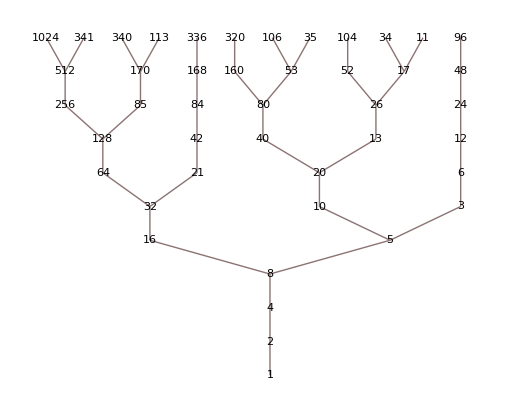

```mathematica
Network`GraphPlot`ExprTreePlot[CollatzTree3nPlusOne[1,1000000,0,11],Bottom]
```

### How long to reach 1?

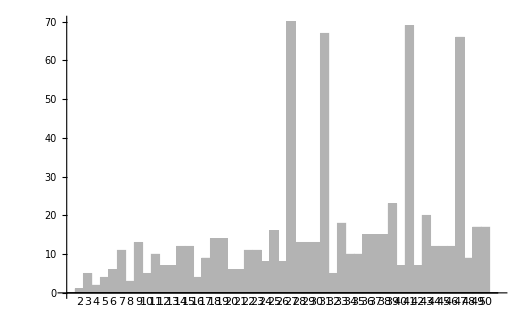

```mathematica
BarChart[Table[Length[NestWhileList[T,n,#1≠1&]]-1,{n,2,50}],PlotTheme->"GrayColor",ChartLabels->{Placed[Style[#,FontSize->Scaled[.012]]&/@Range[2,50],Below]}]
```

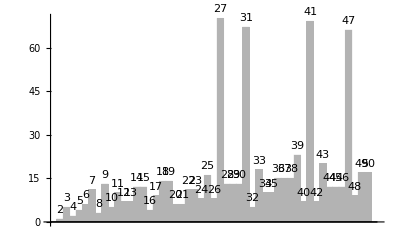

```mathematica
BarChart[Table[Length[NestWhileList[T,n,#1≠1&]]-1,{n,2,50}],PlotTheme->"GrayColor",ChartLabels->{Placed[Style[#,FontSize->Scaled[.015]]&/@Range[2,50],Above]}]
```

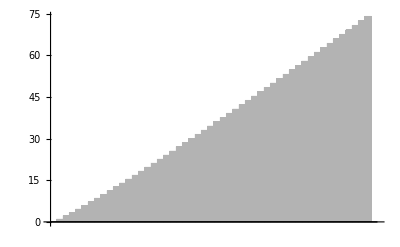

```mathematica
BarChart[Table[n^1.1,{n,1,50}],PlotTheme->"GrayColor"]
```

```mathematica
|
```

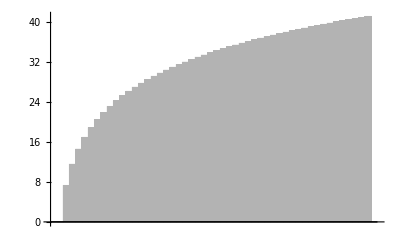

```mathematica
BarChart[Table[Log[1.1,n],{n,1,50}],PlotTheme->"GrayColor"]
```

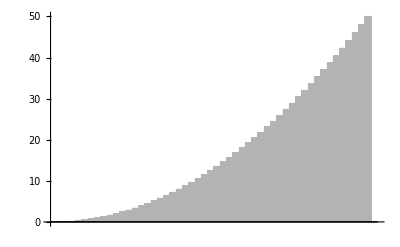

```mathematica
BarChart[Table[n^2/50,{n,1,50}],PlotTheme->"GrayColor"]
```

### Our first pattern

```mathematica
Table[{n,Length[NestWhileList[T,n,#≠1&]]-1},{n,1,51}]
```

{{1,0},{2,1},{3,5},{4,2},{5,4},{6,6},{7,11},{8,3},{9,13},{10,5},{11,10},{12,7},{13,7},{14,12},{15,12},{16,4},{17,9},{18,14},{19,14},{20,6},{21,6},{22,11},{23,11},{24,8},{25,16},{26,8},{27,70},{28,13},{29,13},{30,13},{31,67},{32,5},{33,18},{34,10},{35,10},{36,15},{37,15},{38,15},{39,23},{40,7},{41,69},{42,7},{43,20},{44,12},{45,12},{46,12},{47,66},{48,9},{49,17},{50,17},{51,17}}

```mathematica
NestWhileList[T,49,#≠1&]
```

{49,74,37,56,28,14,7,11,17,26,13,20,10,5,8,4,2,1}

```mathematica
NestWhileList[T,50,#≠1&]
```

{50,25,38,19,29,44,22,11,17,26,13,20,10,5,8,4,2,1}

```mathematica
NestWhileList[T,51,#≠1&]
```

{51,77,116,58,29,44,22,11,17,26,13,20,10,5,8,4,2,1}

```mathematica
NestWhileList[T,28,#≠1&]
```

{28,14,7,11,17,26,13,20,10,5,8,4,2,1}

```mathematica
NestWhileList[T,29,#≠1&]
```

{29,44,22,11,17,26,13,20,10,5,8,4,2,1}

```mathematica
NestWhileList[T,12,#≠1&]
```

{12,6,3,5,8,4,2,1}

```mathematica
NestWhileList[T,13,#1≠1&]
```

{13,20,10,5,8,4,2,1}

```mathematica
NestWhileList[T,20,#≠1&]
```

{20,10,5,8,4,2,1}

```mathematica
NestWhileList[T,21,#≠1&]
```

{21,32,16,8,4,2,1}

### Larger numbers take longer

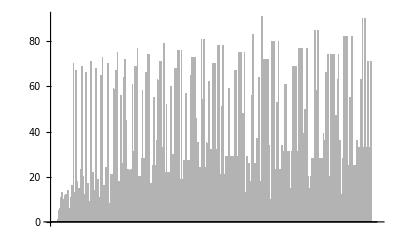

```mathematica
BarChart[Table[Length[NestWhileList[T,n,#1≠1&]]-1,{n,1,500}],PlotTheme->"GrayColor"]
```

```mathematica
Table[{n, Length[NestWhileList[T,n,#1≠1&]]-1},{n,1,500}];
```

### Sequences trend downwards

```mathematica
ToBase10Big[x_]:=IntegerDigits[x,10,225]
```

```mathematica
ArrayPlot[Map[ToBase10Big,b=NestWhileList[T,a=826474739491445506384651754684,#>1&]],ColorRules->{0->White},ColorFunction->"GrayLevel"]
```

ArrayPlot::cfun: Value of option ColorFunction -> GrayLevel is not a valid color function, or a gradient ColorData entity.

-Graphics-

```mathematica
a
```

826474739491445506384651754684

```mathematica
Length[Map[If[EvenQ[#],1,Nothing]&,b]]
```

205

```mathematica
Length[Map[If[OddQ[#],1,Nothing]&,b]]
```

181

### A more organized census

```mathematica
Table[{n,NestList[T,n,4]},{n,0,15}]
```

{{0,{0,0,0,0,0}},{1,{1,2,1,2,1}},{2,{2,1,2,1,2}},{3,{3,5,8,4,2}},{4,{4,2,1,2,1}},{5,{5,8,4,2,1}},{6,{6,3,5,8,4}},{7,{7,11,17,26,13}},{8,{8,4,2,1,2}},{9,{9,14,7,11,17}},{10,{10,5,8,4,2}},{11,{11,17,26,13,20}},{12,{12,6,3,5,8}},{13,{13,20,10,5,8}},{14,{14,7,11,17,26}},{15,{15,23,35,53,80}}}

```mathematica
With[{m=4},Table[If[Or[n<2,Last[NestList[T,n,m]]<n],n,Nothing],{n,0,2^m-1}]]
```

{0,1,3,4,5,6,8,10,12,13}

```mathematica
Table[{2^m,Length[Table[If[Or[n<2,Last[NestList[T,n,m]]<n],True,Nothing],{n,0,2^m-1}]]/2^m*1.},{m,4,16}]
```

{{16,0.625},{32,0.8125},{64,0.640625},{128,0.773438},{256,0.832031},{512,0.746094},{1024,0.827148},{2048,0.725586},{4096,0.805908},{8192,0.866577},{16384,0.787964},{32768,0.849121},{65536,0.894928}}

### Structure

```mathematica
Log[3,2.]
```

0.63093

### Coin flipping

```mathematica
Total[Table[Binomial[10,n],{n,6,10}]]/2^10.
```

0.376953

```mathematica
Total[Table[Binomial[100,n],{n,60,100}]]/2^100.
```

0.028444

```mathematica
SetPrecision[Total[Table[Binomial[1000,n],{n,600,1000}]]/2^1000.,30]
```

1.36423207803300918562884962883×10^-10

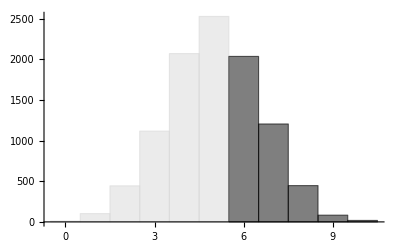

```mathematica
Histogram[{Table[With[{b=Total[Table[RandomInteger[1],{n,1,10}]]},If[b< 6,b,Nothing]],{x,1,10000}],Table[With[{b=Total[Table[RandomInteger[1],{n,1,10}]]},If[b>= 6,b,Nothing]],{x,1,10000}]},{"Raw",800},ChartStyle->{LightGray,Black},Ticks->{{#+.5,#}&/@Range[0,10],Automatic}]
```

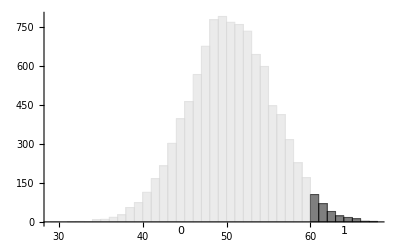

```mathematica
Histogram[{Table[With[{b=Total[Table[RandomInteger[1],{n,1,100}]]},If[b< 60,b,Nothing]],{x,1,10000}],Table[With[{b=Total[Table[RandomInteger[1],{n,1,100}]]},If[b>= 60,b,Nothing]],{x,1,10000}]},{"Raw",800},ChartStyle->{LightGray,Black},ChartLabels->{Placed[Style[#,FontSize->Scaled[.005]]&/@Range[0,100],Below]}]
```

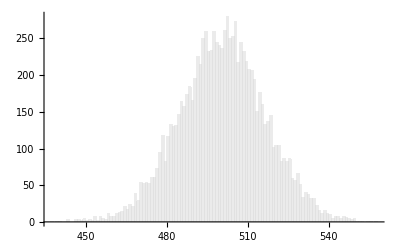

```mathematica
Histogram[{Table[With[{b=Total[Table[RandomInteger[1],{n,1,1000}]]},If[b< 600,b,Nothing]],{x,1,10000}],Table[With[{b=Total[Table[RandomInteger[1],{n,1,1000}]]},If[b>= 600,b,Nothing]],{x,1,10000}]},{"Raw",800},ChartStyle->{LightGray,Black}]
```

### Every operation sequence seen once and only once

```mathematica
Table[{b,(16b-1)/3},{b,1,10}]
```

{{1,5},{2,31/3},{3,47/3},{4,21},{5,79/3},{6,95/3},{7,37},{8,127/3},{9,143/3},{10,53}}

## Chapter 3. Let’s disprove it!

### A heuristic argument

```mathematica
2^20-1
```

1048575

```mathematica
Table[1./2^(y-2),{y,{11,12,13,14,15,20,100}}]
```

{0.00195313,0.000976563,0.000488281,0.000244141,0.00012207,3.8147×10^-6,3.15544×10^-30}

```mathematica
Sum[1./2^(y-2),{y,11,Infinity}]
```

0.00390625

```mathematica
3^7
```

2187

### Where to look for 3n+1 cycles

```mathematica
Denom[k_,x_]:=2^k-3^x
```

```mathematica
Duval1[n_,prev_]:=Take[Flatten[NestList[Join,prev,Ceiling[n/Length[prev]]]],n]
```

```mathematica
Duval2[prev_]:=If[Last[prev]==1,Duval2[Take[prev,Length[prev]-1]],prev]
```

```mathematica
Duval3[prev_]:=ReplacePart[prev,Length[prev]->1]
```

```mathematica
Duval[n_,prev_]:=Duval3[Duval2[Duval1[n,prev]]]
```

```mathematica
Necklaces[k_,x_]:=Map[Reverse,Select[NestWhileList[Duval[k,#]&,{0},#!={1}&],Total[#]==x&&Length[#]==k&]]
```

```mathematica
Necklaces[5,3]
```

{{1,1,1,0,0},{1,1,0,1,0}}

```mathematica
Necklaces[8,5]
```

{{1,1,1,1,1,0,0,0},{1,1,1,1,0,1,0,0},{1,1,1,0,1,1,0,0},{1,1,0,1,1,1,0,0},{1,0,1,1,1,1,0,0},{1,1,1,0,1,0,1,0},{1,1,0,1,1,0,1,0}}

```mathematica
BetaAnd[l_,i_,x_]:=If[Last[Take[l]]==1,2^(i-1)*3^(x-Count[l,1]),0]
```

```mathematica
BetaValue[necklace_]:=Total[Table[BetaAnd[Take[necklace,i],i,Count[necklace,1]],{i,1,Length[necklace]}]]
```

```mathematica
Map[BetaValue,Necklaces[5,3]]
```

{19,23}

```mathematica
LoopsByMember[k_,x_]:=Map[BetaValue[#]/Denom[k,x]&,Necklaces[k,x]]
```

```mathematica
LoopsByMember[5,3]
```

{19/5,23/5}

```mathematica
Map[{BetaValue[#],#}&,Necklaces[5,3]]
```

{{19,{1,1,1,0,0}},{23,{1,1,0,1,0}}}

```mathematica
LoopForOperationSequence[n_,seq_,res_]:=If[seq=={},Reverse[res],If[First[seq]==0,LoopForOperationSequence[n/2,Rest[seq],Insert[res,n/2,1]],LoopForOperationSequence[(3n+1)/2,Rest[seq],Insert[res,(3n+1)/2,1]]]]
```

```mathematica
LoopForOperationSequence[19/5,{1,1,1,0,0},{19/5}]
```

{19/5,31/5,49/5,76/5,38/5,19/5}

```mathematica
LoopForOperationSequence[23/5,{1,1,0,1,0},{23/5}]
```

{23/5,37/5,58/5,29/5,46/5,23/5}

### How many shots do we get?

```mathematica
Necklaces[8,5]
```

{{1,1,1,1,1,0,0,0},{1,1,1,1,0,1,0,0},{1,1,1,0,1,1,0,0},{1,1,0,1,1,1,0,0},{1,0,1,1,1,1,0,0},{1,1,1,0,1,0,1,0},{1,1,0,1,1,0,1,0}}

```mathematica
CountNecklaces[k_,x_]:=(1/k) Sum[MoebiusMu[j] * Binomial[k/j,x/j],{j,Divisors[GCD[k,x]]}]
```

```mathematica
Table[With[{k=kx[[1]],x=kx[[2]]},{k,x,CountNecklaces[k,x],1.000000000000000000*Binomial[k,x]/k}],{kx,{{6,4},{10,7},{19,12},{42,27}}}]
```

{{6,4,2,2.5},{10,7,12,12.},{19,12,2652,2652.},{42,27,2349343467,2.34934351466666667×10^9}}

### Expected number of cycles

```mathematica
1.-4/5 * 4/5
```

0.36

```mathematica
ExactTotalNecklaces[k_,x_]:=If[k==1,1,(1/k)Total[Map[MoebiusMu[#]*Binomial[k/#,x/#]&,Divisors[GCD[k,x]]]]]
```

```mathematica
ExpectedNumberOfCycles[q_,k_]:=ExactTotalNecklaces[k,Floor[k/Log[2,q]]]/Denom[q,k]
```

```mathematica
ExpectedNumberOfCycles[3,8]
```

-7/6553

```mathematica
ApproxTotalNecklaces[k_,x_]:=If[k==1,1,1.0*Binomial[k,x]/k]
```

```mathematica
ApproxTotalNecklaces[5,3]
```

2.

```mathematica
GenDenom[q_,k_]:=If[k==1,100000,2^k-q^Floor[k/Log[2,q]]]
```

```mathematica
ProbOfCycle[q_,k_]:=If[ApproxTotalNecklaces[k,Floor[k/Log[2,q]]]==0,0.0,1.-(1-1/GenDenom[q,k])^ApproxTotalNecklaces[k,Floor[k/Log[2,q]]]]
```

```mathematica
ProbOfCycle[3,5]
```

0.36

```mathematica
ExpectedNumberOfCycles[q_,k_]:=ApproxTotalNecklaces[k,Floor[k/Log[2,q]]]/GenDenom[q,k]
```

```mathematica
ExpectedNumberOfCycles[3,5]
```

0.4

```mathematica
ExpectedNumberOfCycles[3,1000]*1.
```

5.77713×10^-20

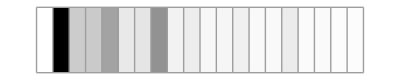

```mathematica
ArrayPlot[Table[ProbOfCycle[2a+1,k],{a,1,1},{k,1,20}],Mesh->All]
```

3n+1

```mathematica
Table[{k,Floor[k/Log[2,3]]},{k,5,10}]
```

{{5,3},{6,3},{7,4},{8,5},{9,5},{10,6}}

```mathematica
Table[{k,ExpectedNumberOfCycles[2a+1,k]*1., ProbOfCycle[2a+1,k]},{a,1,1},{k,5,10}]
```

{{{5,0.4,0.36},{6,0.0900901,0.0872835},{7,0.106383,0.101951},{8,0.538462,0.428962},{9,0.0520446,0.0508055},{10,0.0711864,0.0688244}}}

```mathematica
Table[{k,ExpectedNumberOfCycles[2a+1,k]*1., ProbOfCycle[2a+1,k]*1.},{a,1,1},{k,100,100}]
```

{{{100,0.000277849,0.}}}

```mathematica
Table[{k,ExpectedNumberOfCycles[2a+1,k]*1., ProbOfCycle[2a+1,k]*1.},{a,1,1},{k,1000,1000}]
```

{{{1000,5.77713×10^-20,0.}}}

### Total expected cycles

```mathematica
Map[Total[#]&, Table[ExpectedNumberOfCycles[2a+1,k]*1.,{a,1,1},{k,5,20}]]
```

{1.57009}

```mathematica
Map[Total,Table[ExpectedNumberOfCycles[2a+1,k]*1.,{a,1,1},{k,5,100}]]
```

{1.85859}

```mathematica
Map[Total,Table[ExpectedNumberOfCycles[2a+1,k]*1.,{a,1,1},{k,5,1000}]]
```

{1.86157}

```mathematica
Map[Total,Table[ExpectedNumberOfCycles[2a+1,k]*1.,{a,1,1},{k,5,10000}]]
```

General::munfl: (1.87131×10^303)/(50185005731999307889211120377764226452333042175531579347899764«200»03037455857798286559725298575542340836283453254947474421575847) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.96543×10^303)/(69594115873073676326635222445725756537176466620937890700938749«200»74034158239736398757165766981316987924825306534011458890748405) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.69672×10^303)/(46860544973372534297909389962043423971884080051499977417295163«200»51946056051892274427477043453330894606425813140372447924286943) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.86157}

```mathematica
Sum[(Sqrt[2 Pi k]/(Sqrt[2 Pi(k/Log[2,3])] Sqrt[2 Pi (k - (k/Log[2,3]))]))*((k/E)^k /(((k/Log[2,3])/E)^(k/Log[2,3]) * ((k-k/Log[2,3])/E)^(k-k/Log[2,3])))/(k 2^k),{k,1,100}]*1.
```

1.65515

```mathematica
Simplify[(((k/2.7182818284)^k  Sqrt[2 3.1415926535k])/
(((k/1.5849625007211563)/2.7182818284)^(k/1.5849625007211563) * 
Sqrt[2 Pi(k/1.5849625007211563)]*
((k-k/1.5849625007211563)/2.7182818284)^(k-k/1.5849625007211563) * 
Sqrt[2 Pi (k-(k/1.5849625007211563))]))/(k 2^k)]
```

(0.826733 ⅇ^(-0.0346882 k))/k^1.5

```mathematica
E^-0.034688
```

0.965907

```mathematica
Sum[(0.82673 * 0.96591^k)/(k Sqrt[k]),{k,1,Infinity}]
```

1.6557

## Chapter 4. The qn+1 problem

### Where to look for 3n-1 cycles

```mathematica
NegDenom[q_,k_]:=If[(k==1)&&(q>3),100000,2^k-q^Ceiling[k/Log[2,q]]]
```

```mathematica
NegExpectedNumberOfCycles[q_,k_]:=-ExactTotalNecklaces[k,Ceiling[k/Log[2,q]]]/NegDenom[q,k]
```

```mathematica
NegProbOfCycle[q_,k_]:=If[ExactTotalNecklaces[k,Ceiling[k/Log[2,q]]]==0,0.0,1.-(1-1/-NegDenom[q,k])^ExactTotalNecklaces[k,Ceiling[k/Log[2,q]]]]
```

```mathematica
Table[{k,Ceiling[k/Log[2,3]]},{k,5,10}]
```

{{5,4},{6,4},{7,5},{8,6},{9,6},{10,7}}

```mathematica
Table[{k, NegExpectedNumberOfCycles[2a+1,k]*1.,NegProbOfCycle[2a+1,k]},{a,1,1},{k,5,20}]
```

{{{5,0.0204082,0.0204082},{6,0.117647,0.114187},{7,0.026087,0.0258608},{8,0.00634249,0.0063291},{9,0.0414747,0.0407183},{10,0.0103181,0.0102695},{11,0.215827,0.194754},{12,0.0162272,0.0160995},{13,0.00478635,0.00477513},{14,0.0433465,0.0424267},{15,0.00761006,0.00758132},{16,0.002446,0.00244302},{17,0.0158003,0.0156763},{18,0.00380992,0.00380268},{19,0.370754,0.309804},{20,0.00710219,0.00707704}}}

### The 3n-1 tree

```mathematica
CollatzTree3nMinusOne[n_,cutoff_,height_,depth_]:=
If[(depth==1)||(n>cutoff),n,
If[2n>cutoff,
If[(n>2)&&(Mod[n,3]==1),
n[CollatzTree3nMinusOne[(2n+1)/3,cutoff,If[OddQ[n],height+1,height],depth-1]],n],
If[(n>2)&&(n!=7)&&(Mod[n,3]==1),
n[CollatzTree3nMinusOne[(2n+1)/3,cutoff,If[OddQ[n],height+1,height],depth-1],
CollatzTree3nMinusOne[2n,cutoff,If[OddQ[n],height+1,height],depth-1]],
n[CollatzTree3nMinusOne[2n,cutoff,If[OddQ[n],height+1,height],depth-1]]]]]
```

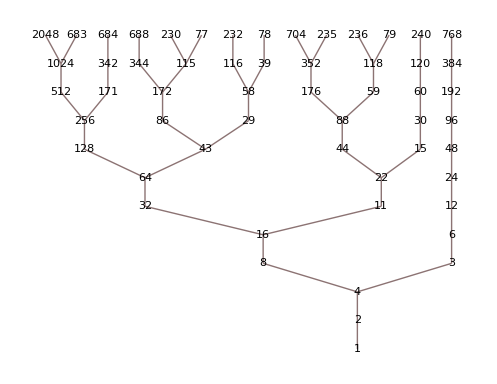

```mathematica
Network`GraphPlot`ExprTreePlot[CollatzTree3nMinusOne[1,100000,0,12],Bottom]
```

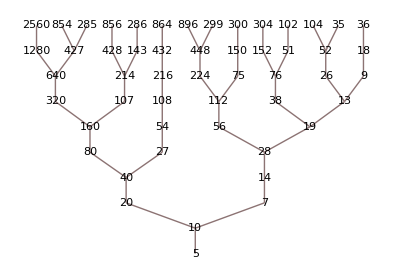

-Graphics-

```mathematica
Network`GraphPlot`ExprTreePlot[CollatzTree3nMinusOne[5,100000,0,10],Bottom]
```

### The 5n+1 problem

```mathematica
Table[{k,Floor[k/Log[2,5]]},{k,5,10}]
```

{{5,2},{6,2},{7,3},{8,3},{9,3},{10,4}}

```mathematica
Table[{k,ExpectedNumberOfCycles[2a+1,k]*1., ProbOfCycle[2a+1,k]},{a,2,2},{k,5,14}]
```

{{{5,0.285714,0.265306},{6,0.0641026,0.0628751},{7,1.66667,0.868313},{8,0.0534351,0.0522269},{9,0.0241171,0.0238591},{10,0.0526316,0.0513332},{11,0.0210822,0.0208688},{12,0.0679712,0.0657453},{13,0.0195382,0.0193504},{14,0.282609,0.246326}}}

```mathematica
T5[n_]:=If[EvenQ[n],n/2,(5n+1)/2]
```

```mathematica
NestList[T5,13,7]
```

{13,33,83,208,104,52,26,13}

```mathematica
NestList[T5,17,7]
```

{17,43,108,54,27,68,34,17}

```mathematica
CollatzTree5nPlusOne[n_,cutoff_,height_,depth_]:=
If[(depth==1)||(n>cutoff),n,
If[2n>cutoff,
If[(n>2)&&(Mod[n,5]==3),
n[CollatzTree5nPlusOne[(2n-1)/5,cutoff,If[OddQ[n],height+1,height],depth-1]],n],
If[(n>2)&&(n!=3)&&(n!=33)&&(n!=43)&&(Mod[n,5]==3),
n[CollatzTree5nPlusOne[(2n-1)/5,cutoff,If[OddQ[n],height+1,height],depth-1],
CollatzTree5nPlusOne[2n,cutoff,If[OddQ[n],height+1,height],depth-1]],
n[CollatzTree5nPlusOne[2n,cutoff,If[OddQ[n],height+1,height],depth-1]]]]]
```

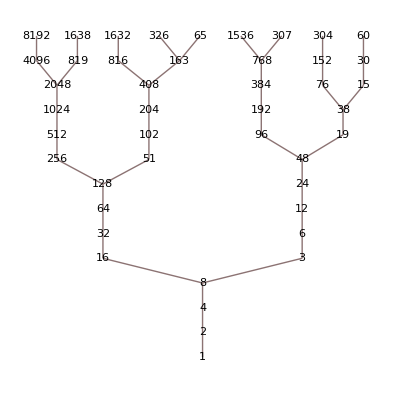

```mathematica
Network`GraphPlot`ExprTreePlot[CollatzTree5nPlusOne[1,1000000,0,14],Bottom]
```

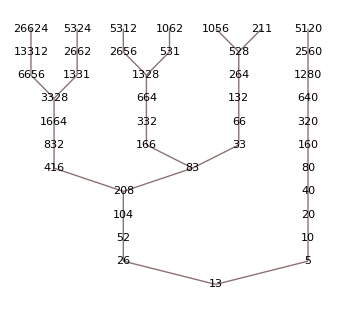

```mathematica
Network`GraphPlot`ExprTreePlot[CollatzTree5nPlusOne[13,1000000,0,12],Bottom]
```

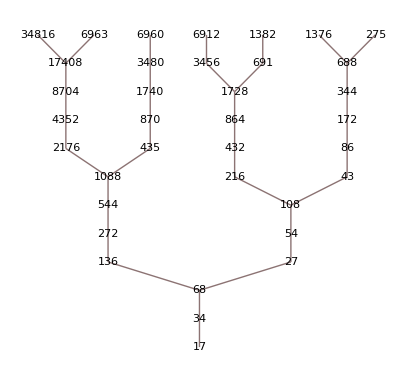

```mathematica
Network`GraphPlot`ExprTreePlot[CollatzTree5nPlusOne[17,1000000,0,12],Bottom]
```

### Cycles for the qn+1 problem

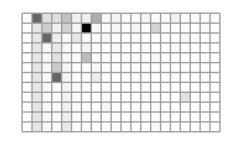

```mathematica
ArrayPlot[Table[ExpectedNumberOfCycles[2a+1,k],{a,1,12},{k,1,20}],Mesh->All]
```

```mathematica
Map[{#[[1]],#[[2]],ExpectedNumberOfCycles[#[[1]],#[[2]]]}&,{{3,2},{3,5},{3,8},{5,7},{7,3},{15,4},{5,14},{11,7}}]
```

{{3,2,1.},{3,5,0.4},{3,8,0.538462},{5,7,1.66667},{7,3,1.},{15,4,1.},{5,14,0.282609},{11,7,0.428571}}

### The start number 1

```mathematica
NestList[If[EvenQ[#],#/2,(9 # + 1)/2]&,1, 20]
```

{1,5,23,104,52,26,13,59,266,133,599,2696,1348,674,337,1517,6827,30722,15361,69125,311063}

```mathematica
NestList[If[EvenQ[#],#/2,(90 # + 1)/2]&,1, 20]
```

{1,91/2,2048,1024,512,256,128,64,32,16,8,4,2,1,91/2,2048,1024,512,256,128,64}

```mathematica
NestList[If[EvenQ[#],#/2,(2 # + 1)/2]&,1, 20]
```

{1,3/2,2,1,3/2,2,1,3/2,2,1,3/2,2,1,3/2,2,1,3/2,2,1,3/2,2}

```mathematica
NestList[If[EvenQ[#],#/2,(16# + 1)/2]&,1, 20]
```

{1,17/2,137/2,1097/2,8777/2,70217/2,561737/2,4493897/2,35951177/2,287609417/2,2300875337/2,18407002697/2,147256021577/2,1178048172617/2,9424385380937/2,75395083047497/2,603160664379977/2,4825285315039817/2,38602282520318537/2,308818260162548297/2,2470546081300386377/2}

### The 181n+1 problem

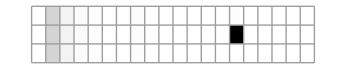

```mathematica
ArrayPlot[Table[ExpectedNumberOfCycles[2a+1,k],{a,89,91},{k,1,20}],Mesh->All]
```

```mathematica
ExpectedNumberOfCycles[181,15]
```

1.

```mathematica
ProbOfCycle[181,15]
```

0.660083

```mathematica
{2^15,181^2}
```

{32768,32761}

```mathematica
NestList[If[EvenQ[#],#/2,(181 # + 1)/2]&,27, 15]
```

{27,2444,1222,611,55296,27648,13824,6912,3456,1728,864,432,216,108,54,27}

### The 1093+1 problem

```mathematica
NestList[If[EvenQ[#],#/2,(7 # + 1)/2]&,3, 33]
```

{3,11,39,137,480,240,120,60,30,15,53,186,93,326,163,571,1999,6997,24490,12245,42858,21429,75002,37501,131254,65627,229695,803933,2813766,1406883,4924091,17234319,60320117,211120410}

```mathematica
C1093[n_]:=If[EvenQ[n],n/2,(1093n+1)/2]
```

```mathematica
NestList[C1093,3,10]
```

{3,1640,820,410,205,112033,61226035,33460028128,16730014064,8365007032,4182503516}

### Height

```mathematica
Uaux[n_,q_,a_]:=If[EvenQ[n],Uaux[n/2,q,1],If[a==1,n,Uaux[q*n+1,q,1]]]
```

```mathematica
U[n_,q_]:=Uaux[n,q,0]
```

```mathematica
NestWhileList[U[#,3]&,27,#!=1&]
```

{27,41,31,47,71,107,161,121,91,137,103,155,233,175,263,395,593,445,167,251,377,283,425,319,479,719,1079,1619,2429,911,1367,2051,3077,577,433,325,61,23,35,53,5,1}

```mathematica
height[n_,q_]:=Length[NestWhileList[U[#,q]&,n,#!=1&]]-1
```

```mathematica
height[27,3]
```

41

```mathematica
Solve[Mod[2^(m+1)-1,3]==0,{m},Integers]
```

{{m→ConditionalExpression[1+2 C[1], C[1]∈ℤ&&C[1]≥-1]}}

```mathematica
Table[(4^m-1)/3,{m,0,10}]
```

{0,1,5,21,85,341,1365,5461,21845,87381,349525}

```mathematica
Solve[Mod[2^m-5,9]==0,{m},Integers]
```

{{m→ConditionalExpression[5+6 C[1], C[1]∈ℤ&&C[1]≥0]}}

```mathematica
Table[(2^(5+6m)-5)/9,{m,0,10}]
```

{3,227,14563,932067,59652323,3817748707,244335917283,15637498706147,1000799917193443,64051194700380387,4099276460824344803}

```mathematica
Limit[(3x)/(4^x-1),{x->Infinity}]
```

0

### No height-2 numbers for 1093n+1

```mathematica
Solve[Mod[2^(m+1)-1,1093]==0,{m},Integers]
```

{{m→ConditionalExpression[363+364 C[1], C[1]∈ℤ&&C[1]≥-1]}}

```mathematica
Solve[1093n==2^364-1,{n},Integers]
```

{{n→34379397369058857864804839477245555752983459087404499479704167927278448675053737507245365026675479641821555}}

```mathematica
height[34379397369058857864804839477245555752983459087404499479704167927278448675053737507245365026675479641821555,1093]
```

1

```mathematica
Table[Mod[2^(364a)-1,1093],{a,2,10}]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
Table[Mod[2^(364a)-1,1093^2],{a,2,10}]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
MultiplicativeOrder[2,1093]
```

364

```mathematica
MultiplicativeOrder[2,1093^2]
```

364

```mathematica
Map[If[MultiplicativeOrder[2,#]==MultiplicativeOrder[2,#^2],#,Nothing]&,Table[Prime[n], {n,2,500}]]
```

{1093,3511}

```mathematica
MultiplicativeOrder[2,3511]
```

1755

```mathematica
MultiplicativeOrder[2,3511^2]
```

1755

```mathematica
MultiplicativeOrder[3,11]
```

5

```mathematica
Table[Mod[3^x,11],{x,1,20}]
```

{3,9,5,4,1,3,9,5,4,1,3,9,5,4,1,3,9,5,4,1}

```mathematica
MultiplicativeOrder[2,11]
```

10

## Chapter 5. Circuit cycles

### Enumerating all possible circuits

```mathematica
Grid[Table[2^a 2^x-3^x,{x,1,6},{a,0,6}]]
```

-1 | 1 | 5 | 13 | 29 | 61 | 125
-5 | -1 | 7 | 23 | 55 | 119 | 247
-19 | -11 | 5 | 37 | 101 | 229 | 485
-65 | -49 | -17 | 47 | 175 | 431 | 943
-211 | -179 | -115 | 13 | 269 | 781 | 1805
-665 | -601 | -473 | -217 | 295 | 1319 | 3367

```mathematica
Format[primeFactorForm[n_Integer]]:=CenterDot@@Superscript@@@FactorInteger[n]/. _[x_]:>x
```

```mathematica
Grid[Table[primeFactorForm[2^a 2^x-3^x],{x,1,6},{a,0,6}]]
```

(-1)^1 | 1^1 | 5^1 | 13^1 | 29^1 | 61^1 | 5^3
(-1)^1·5^1 | (-1)^1 | 7^1 | 23^1 | 5^1·11^1 | 7^1·17^1 | 13^1·19^1
(-1)^1·19^1 | (-1)^1·11^1 | 5^1 | 37^1 | 101^1 | 229^1 | 5^1·97^1
(-1)^1·5^1·13^1 | (-1)^1·7^2 | (-1)^1·17^1 | 47^1 | 5^2·7^1 | 431^1 | 23^1·41^1
(-1)^1·211^1 | (-1)^1·179^1 | (-1)^1·5^1·23^1 | 13^1 | 269^1 | 11^1·71^1 | 5^1·19^2
(-1)^1·5^1·7^1·19^1 | (-1)^1·601^1 | (-1)^1·11^1·43^1 | (-1)^1·7^1·31^1 | 5^1·59^1 | 1319^1 | 7^1·13^1·37^1

```mathematica
ArrayPlot[Table[If[(2^x 2^b-3^x>0)&&(3^x-2^x)>=(2^x 2^b - 3^x),0,1],{x,1,70},{b,1,70}]]
```

-Graphics-

### A systematic approach

```mathematica
With[{p=5},ArrayPlot[Table[With[{k=x+y},If[Divisible[2^k-3^x,p]&&Not[Divisible[3^x-2^x,p]],1,0]],{x,1,20},{y,1,20}],{Mesh->Automatic}]]
```

-Graphics-

```mathematica
With[{p=7},ArrayPlot[Table[With[{k=x+y},If[Divisible[2^k-3^x,p]&&Not[Divisible[3^x-2^x,p]],1,0]],{x,1,20},{y,1,20}],{Mesh->Automatic}]]
```

-Graphics-

```mathematica
With[{p=11},ArrayPlot[Table[With[{k=x+y},If[Divisible[2^k-3^x,p]&&Not[Divisible[3^x-2^x,p]],1,0]],{x,1,20},{y,1,20}],{Mesh->Automatic}]]
```

-Graphics-

```mathematica
With[{p=13},ArrayPlot[Table[With[{k=x+y},If[Divisible[2^k-3^x,p]&&Not[Divisible[3^x-2^x,p]],1,0]],{x,1,20},{y,1,20}],{Mesh->Automatic}]]
```

-Graphics-

```mathematica
ArrayPlot[Table[With[{k=x+y},If[Or[Divisible[2^k-3^x,5]&&Not[Divisible[3^x-2^x,5]],Divisible[2^k-3^x,7]&&Not[Divisible[3^x-2^x,7]],Divisible[2^k-3^x,11]&&Not[Divisible[3^x-2^x,11]],Divisible[2^k-3^x,13]&&Not[Divisible[3^x-2^x,13]]],1,0]],{x,1,20},{y,1,20}],{Mesh->Automatic}]
```

-Graphics-

```mathematica
Length[Flatten[Table[With[{k=x+y},If[Or[Divisible[2^k-3^x,5]&&Not[Divisible[3^x-2^x,5]],Divisible[2^k-3^x,7]&&Not[Divisible[3^x-2^x,7]],Divisible[2^k-3^x,11]&&Not[Divisible[3^x-2^x,11]],Divisible[2^k-3^x,13]&&Not[Divisible[3^x-2^x,13]]],1,0]],{x,1,100},{y,1,100}]]]
```

10000

```mathematica
Length[Flatten[Table[With[{k=x+y},If[Or[Divisible[2^k-3^x,5]&&Not[Divisible[3^x-2^x,5]],Divisible[2^k-3^x,7]&&Not[Divisible[3^x-2^x,7]],Divisible[2^k-3^x,11]&&Not[Divisible[3^x-2^x,11]],Divisible[2^k-3^x,13]&&Not[Divisible[3^x-2^x,13]]],1,Nothing]],{x,1,100},{y,1,100}]]]
```

3709

```mathematica
3709./10000
```

0.3709

## Chapter 6. Ready for prime time

### Prime factors

```mathematica
FactorInteger[46189]
```

{{11,1},{13,1},{17,1},{19,1}}

```mathematica
FactorInteger[3553]
```

{{11,1},{17,1},{19,1}}

```mathematica
46189/3553
```

13

```mathematica
Map[FactorInteger,{20,21,22,23,88,89,90,91,131,132,133,134}]
```

{{{2,2},{5,1}},{{3,1},{7,1}},{{2,1},{11,1}},{{23,1}},{{2,3},{11,1}},{{89,1}},{{2,1},{3,2},{5,1}},{{7,1},{13,1}},{{131,1}},{{2,2},{3,1},{11,1}},{{7,1},{19,1}},{{2,1},{67,1}}}

### Prime chaos

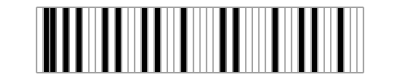

```mathematica
ArrayPlot[Table[If[PrimeQ[50*x+y+1],1,0],{x,0,0},{y,0,49}],{Mesh->True}]
```

```mathematica
ArrayPlot[Table[If[PrimeQ[50*x+y+1],1,0],{x,0,19},{y,0,49}],{Mesh->True}]
```

-Graphics-

### Prime patterns

```mathematica
ArrayPlot[Table[If[PrimeQ[50*x+y+1],1,0],{x,10000,10019},{y,0,49}],{Mesh->True}]
```

-Graphics-

```mathematica
ArrayPlot[Table[If[PrimeQ[50*x+y+1],1,0],{x,1000000000,1000000019},{y,0,49}],{Mesh->True}]
```

-Graphics-

### Primes are never ending

```mathematica
{2*3*7*43+1,FactorInteger[2*3*7*43+1]}
```

{1807,{{13,1},{139,1}}}

### Counting the primes between 1 and n

```mathematica
Primorial[n_]:=Product[Prime[i],{i,1,n}]
```

```mathematica
Primorial[3]
```

30

```mathematica
ActualPrimesUpToPrimorial[m_]:=Map[If[PrimeQ[#],#,Nothing]&,Range[1,Primorial[m]]]
```

```mathematica
ActualPrimesUpToPrimorial[4]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199}

```mathematica
Length[ActualPrimesUpToPrimorial[4]]
```

46

```mathematica
PossiblePrimesUpToPrimorial[m_]:= pputp[Table[Prime[n],{n,m}],Range[2,Primorial[m]]]
```

```mathematica
pputp[primes_,result_]:=If[primes=={},result,pputp[Rest[primes],Map[If[(#!=First[primes])&&Divisible[#,First[primes]],Nothing,#]&,result]]]
```

```mathematica
PossiblePrimesUpToPrimorial[4]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,121,127,131,137,139,143,149,151,157,163,167,169,173,179,181,187,191,193,197,199,209}

```mathematica
Length[PossiblePrimesUpToPrimorial[4]]
```

51

```mathematica
Complement[PossiblePrimesUpToPrimorial[4],ActualPrimesUpToPrimorial[4]]
```

{121,143,169,187,209}

```mathematica
FactorInteger[143]
```

{{11,1},{13,1}}

```mathematica
MaxPrimesUpToPrimorialPart1[m_]:=(m-1)/Primorial[m]
```

```mathematica
MaxPrimesUpToPrimorialPart2[m_] := Product[(Prime[i]-1)/Prime[i],{i,1,m}]
```

```mathematica
MaxPrimesUpToPrimorial[m_]:=MaxPrimesUpToPrimorialPart1[m]+MaxPrimesUpToPrimorialPart2[m]
```

```mathematica
Table[{i,1.*MaxPrimesUpToPrimorialPart1[i]},{i,1,10}]
```

{{1,0.},{2,0.166667},{3,0.0666667},{4,0.0142857},{5,0.0017316},{6,0.0001665},{7,0.000011753},{8,7.21673×10^-7},{9,3.58595×10^-8},{10,1.3911×10^-9}}

```mathematica
Table[{i,1.*MaxPrimesUpToPrimorialPart2[10^i]},{i,1,5}]
```

{{1,0.157947},{2,0.0887499},{3,0.0624666},{4,0.048559},{5,0.0398807}}

```mathematica
Table[{i,1.*MaxPrimesUpToPrimorial[10^i]},{i,1,5}]
```

{{1,0.157947},{2,0.0887499},{3,0.0624666},{4,0.048559},{5,0.0398807}}

```mathematica
Table[{i,1.*MaxPrimesUpToPrimorial[i]*Primorial[i]},{i,1,20}]
```

{{1,1.},{2,3.},{3,10.},{4,51.},{5,484.},{6,5765.},{7,92166.},{8,1.65889×10^6},{9,3.64954×10^7},{10,1.02187×10^9},{11,3.06561×10^10},{12,1.10362×10^12},{13,4.41448×10^13},{14,1.85408×10^15},{15,8.52877×10^16},{16,4.43496×10^18},{17,2.57228×10^20},{18,1.54337×10^22},{19,1.01862×10^24},{20,7.13035×10^25}}

```mathematica
Table[Product[(10^i-1)/10.^i,{i,1,n}],{n,1,10}]
```

{0.9,0.891,0.890109,0.89002,0.890011,0.89001,0.89001,0.89001,0.89001,0.89001}

### How fast do primes thin out?

Counting powers of 2 between 1 and 10^y

```mathematica
Table[With[{x=Range[10^y]},{y,Count[x,n_/;IntegerQ[Log[2,n]]]}],{y,1,6}]
```

{{1,4},{2,7},{3,10},{4,14},{5,17},{6,20}}

Counting perfect squares

```mathematica
Table[With[{x=Range[10^y]},{y,Count[x,n_/;IntegerQ[Sqrt[n]]]}],{y,1,6}]
```

{{1,3},{2,10},{3,31},{4,100},{5,316},{6,1000}}

Counting primes

```mathematica
Table[With[{x=Range[10^y]},{y,Count[x,n_/;PrimeQ[n]]}],{y,1,6}]
```

{{1,4},{2,25},{3,168},{4,1229},{5,9592},{6,78498}}

```mathematica
Table[{digits,Length[Table[If[PrimeQ[x],x,Nothing],{x,10^(digits-1),10^digits-1}]]/(10^digits-10^(digits-1)+1.)},{digits,2,6}]
```

{{2,0.230769},{3,0.158713},{4,0.117876},{5,0.0929212},{6,0.0765621}}

```mathematica
Table[{x,(1/x)*0.4545},{x,2,8}]
```

{{2,0.22725},{3,0.1515},{4,0.113625},{5,0.0909},{6,0.07575},{7,0.0649286},{8,0.0568125}}

### Logarithms

```mathematica
SetPrecision[Log[10,500.],10]
```

2.698970004

```mathematica
SetPrecision[Log[10,50.],10]
```

1.698970004

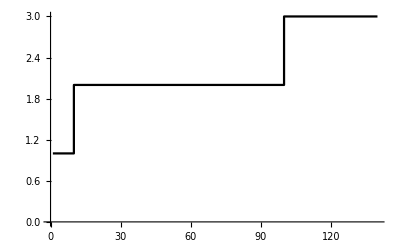

```mathematica
jaggedplot= ListStepPlot[{{1,1},{10,2},{100,3},{120,3}},PlotStyle->{Black}];
```

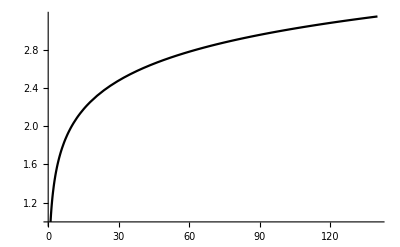

```mathematica
smoothedplot=Plot[Log[10.,x]+1,{x,1,140},PlotTheme->"GrayColor"];
```

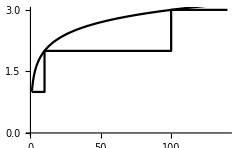

```mathematica
Show[jaggedplot,smoothedplot]
```

```mathematica
Table[{x,Log[10.,x]+1,Floor[Log[10.,x]]+1},{x,1,120}]
```

{{1,1.,1},{2,1.30103,1},{3,1.47712,1},{4,1.60206,1},{5,1.69897,1},{6,1.77815,1},{7,1.8451,1},{8,1.90309,1},{9,1.95424,1},{10,2.,2},{11,2.04139,2},{12,2.07918,2},{13,2.11394,2},{14,2.14613,2},{15,2.17609,2},{16,2.20412,2},{17,2.23045,2},{18,2.25527,2},{19,2.27875,2},{20,2.30103,2},{21,2.32222,2},{22,2.34242,2},{23,2.36173,2},{24,2.38021,2},{25,2.39794,2},{26,2.41497,2},{27,2.43136,2},{28,2.44716,2},{29,2.4624,2},{30,2.47712,2},{31,2.49136,2},{32,2.50515,2},{33,2.51851,2},{34,2.53148,2},{35,2.54407,2},{36,2.5563,2},{37,2.5682,2},{38,2.57978,2},{39,2.59106,2},{40,2.60206,2},{41,2.61278,2},{42,2.62325,2},{43,2.63347,2},{44,2.64345,2},{45,2.65321,2},{46,2.66276,2},{47,2.6721,2},{48,2.68124,2},{49,2.6902,2},{50,2.69897,2},{51,2.70757,2},{52,2.716,2},{53,2.72428,2},{54,2.73239,2},{55,2.74036,2},{56,2.74819,2},{57,2.75587,2},{58,2.76343,2},{59,2.77085,2},{60,2.77815,2},{61,2.78533,2},{62,2.79239,2},{63,2.79934,2},{64,2.80618,2},{65,2.81291,2},{66,2.81954,2},{67,2.82607,2},{68,2.83251,2},{69,2.83885,2},{70,2.8451,2},{71,2.85126,2},{72,2.85733,2},{73,2.86332,2},{74,2.86923,2},{75,2.87506,2},{76,2.88081,2},{77,2.88649,2},{78,2.89209,2},{79,2.89763,2},{80,2.90309,2},{81,2.90849,2},{82,2.91381,2},{83,2.91908,2},{84,2.92428,2},{85,2.92942,2},{86,2.9345,2},{87,2.93952,2},{88,2.94448,2},{89,2.94939,2},{90,2.95424,2},{91,2.95904,2},{92,2.96379,2},{93,2.96848,2},{94,2.97313,2},{95,2.97772,2},{96,2.98227,2},{97,2.98677,2},{98,2.99123,2},{99,2.99564,2},{100,3.,3},{101,3.00432,3},{102,3.0086,3},{103,3.01284,3},{104,3.01703,3},{105,3.02119,3},{106,3.02531,3},{107,3.02938,3},{108,3.03342,3},{109,3.03743,3},{110,3.04139,3},{111,3.04532,3},{112,3.04922,3},{113,3.05308,3},{114,3.0569,3},{115,3.0607,3},{116,3.06446,3},{117,3.06819,3},{118,3.07188,3},{119,3.07555,3},{120,3.07918,3}}

```mathematica
Log[10.,e]
```

0.434294 Log[e]

## Chapter 7. Back to the conjecture

### If it were a whole number

```mathematica
Log[10,2^1000-1.]
```

301.03

```mathematica
NestList[#/2&,2^8,8]
```

{256,128,64,32,16,8,4,2,1}

```mathematica
NestList[(3#+1)/2&, 2^8-1,8]
```

{255,383,575,863,1295,1943,2915,4373,6560}

### Factors of Powers

```mathematica
Table[{x,3^x-2^x,FactorInteger[3^x-2^x]},{x, 1, 10}]
```

{{1,1,{{1,1}}},{2,5,{{5,1}}},{3,19,{{19,1}}},{4,65,{{5,1},{13,1}}},{5,211,{{211,1}}},{6,665,{{5,1},{7,1},{19,1}}},{7,2059,{{29,1},{71,1}}},{8,6305,{{5,1},{13,1},{97,1}}},{9,19171,{{19,1},{1009,1}}},{10,58025,{{5,2},{11,1},{211,1}}}}

### Modular arithmetic

```mathematica
Table[Mod[2^x,Prime[p]],{p,3,8},{x,1,14}]
```

{{2,4,3,1,2,4,3,1,2,4,3,1,2,4},{2,4,1,2,4,1,2,4,1,2,4,1,2,4},{2,4,8,5,10,9,7,3,6,1,2,4,8,5},{2,4,8,3,6,12,11,9,5,10,7,1,2,4},{2,4,8,16,15,13,9,1,2,4,8,16,15,13},{2,4,8,16,13,7,14,9,18,17,15,11,3,6}}

### Modular chaos

```mathematica
p=7933
```

7933

```mathematica
PrimitiveRoot[7933]
```

2

```mathematica
Mod[2^1239,7933]
```

1399

```mathematica
Table[{2^x,Mod[2^(2^x),7933]},{x,1,10}]
```

{{2,4},{4,16},{8,256},{16,2072},{32,1431},{64,1047},{128,1455},{256,6847},{512,5312},{1024,7596}}

```mathematica
Mod[7596*1455*1047*2072*16*4*2,7933]
```

1399

```mathematica
Position[Table[Mod[2^x,p],{x,1,p}],4621]
```

{{999}}

```mathematica
Table[Mod[2^x,7933],{x,1,20}]
```

{2,4,8,16,32,64,128,256,512,1024,2048,4096,259,518,1036,2072,4144,355,710,1420}

### Internet security

```mathematica
public = 7933
```

7933

```mathematica
PrimitiveRoot[public]
```

2

```mathematica
mySecret = 56
```

56

```mathematica
iTextYou = Mod[2^mySecret,public]
```

2886

```mathematica
yourSecret = 327
```

327

```mathematica
youTextMe = Mod[2^yourSecret,public]
```

5375

```mathematica
shared = Mod[youTextMe^mySecret,public]
```

792

```mathematica
shared = Mod[iTextYou^yourSecret,public]
```

792

```mathematica
Mod[(2^327)^56,7933]
```

792

```mathematica
Solve[Mod[2^x,7933]==2886,Integers]
```

{{x→ConditionalExpression[56+7932 C[1], C[1]∈ℤ&&C[1]≥0]}}

```mathematica
Solve[Mod[2^x,7933]==5375,Integers]
```

{{x→ConditionalExpression[327+7932 C[1], C[1]∈ℤ&&C[1]≥0]}}

### Where were we?

```mathematica
Table[Mod[3^x,Prime[p]],{p,3,8},{x,1,14}]
```

{{3,4,2,1,3,4,2,1,3,4,2,1,3,4},{3,2,6,4,5,1,3,2,6,4,5,1,3,2},{3,9,5,4,1,3,9,5,4,1,3,9,5,4},{3,9,1,3,9,1,3,9,1,3,9,1,3,9},{3,9,10,13,5,15,11,16,14,8,7,4,12,2},{3,9,8,5,15,7,2,6,18,16,10,11,14,4}}

### How about the denominator?

```mathematica
FactorInteger[2^72-3^24]
```

{{5,1},{7,2},{11,1},{13,1},{73,1},{97,1},{277,1},{577,1},{4177,1},{28513,1}}

### Column by column

```mathematica
Table[{x,2^(x+3)-3^x},{x, 1, 10}]
```

{{1,13},{2,23},{3,37},{4,47},{5,13},{6,-217},{7,-1163},{8,-4513},{9,-15587},{10,-50857}}

```mathematica
FactorInteger[-217]
```

{{-1,1},{7,1},{31,1}}

### Fourth column

```mathematica
Table[{x,Mod[16*2^x,7],Mod[3^x+5,7]},{x,1,10}]
```

{{1,4,1},{2,1,0},{3,2,4},{4,4,2},{5,1,3},{6,2,6},{7,4,1},{8,1,0},{9,2,4},{10,4,2}}

## Chapter 8. Is it provable?

## Chapter 9. Divisibility by size

```mathematica
Reduce[1.6^x > 2(1.5)^x ,{x},Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x>10.7401

```mathematica
Reduce[3^(x/2)>1.6^x,{x},Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x>0

### A smaller numerator

```mathematica
Table[With[{x=Floor[k/Log[2,3]]},{k, x,3^x-2^x,2^(k-x)-1,2^k-3^x}],{k,5,19}]
```

{{5,3,19,3,5},{6,3,19,7,37},{7,4,65,7,47},{8,5,211,7,13},{9,5,211,15,269},{10,6,665,15,295},{11,6,665,31,1319},{12,7,2059,31,1909},{13,8,6305,31,1631},{14,8,6305,63,9823},{15,9,19171,63,13085},{16,10,58025,63,6487},{17,10,58025,127,72023},{18,11,175099,127,84997},{19,11,175099,255,347141}}

### Co-primes

```mathematica
a=With[{q=68},Table[If[CoprimeQ[x,y],1,0],{x,1,q},{y,1,q}]]; ArrayPlot[a,ColorRules->{0->White,1->Black}]
```

-Graphics-

```mathematica
a=Total[With[{q=68},Flatten[Table[If[CoprimeQ[x,y],1,0],{x,1,q},{y,1,q}]]/(q*q)]]
```

2851/4624

```mathematica
a*1.
```

0.616566

```mathematica
FactorInteger[3787238]
```

{{2,1},{7,1},{13,1},{20809,1}}

### What a bunch of squares have to do with a circle

```mathematica
Table[{n,Sum[1./i^2,{i,1,n}]},{n,1,10}]
```

{{1,1.},{2,1.25},{3,1.36111},{4,1.42361},{5,1.46361},{6,1.49139},{7,1.5118},{8,1.52742},{9,1.53977},{10,1.54977}}

```mathematica
Table[{n,Product[Prime[i]^2./(Prime[i]^2-1),{i,1,n}]},{n,2,10}]
```

{{2,1.5},{3,1.5625},{4,1.59505},{5,1.60834},{6,1.61792},{7,1.62354},{8,1.62805},{9,1.63113},{10,1.63307}}

### Squarefree numbers

```mathematica
HarmonicQ[n_]:=1==Last[NestWhileList[#/3&,With[{h=Last[NestWhileList[#/2&,n,EvenQ]]},h],Mod[#,3]==0&]]
```

```mathematica
HarmonicQ[54]
```

True

```mathematica
Map[If[HarmonicQ[#],#,Nothing]&,Range[1000000]]
```

{1,2,3,4,6,8,9,12,16,18,24,27,32,36,48,54,64,72,81,96,108,128,144,162,192,216,243,256,288,324,384,432,486,512,576,648,729,768,864,972,1024,1152,1296,1458,1536,1728,1944,2048,2187,2304,2592,2916,3072,3456,3888,4096,4374,4608,5184,5832,6144,6561,6912,7776,8192,8748,9216,10368,11664,12288,13122,13824,15552,16384,17496,18432,19683,20736,23328,24576,26244,27648,31104,32768,34992,36864,39366,41472,46656,49152,52488,55296,59049,62208,65536,69984,73728,78732,82944,93312,98304,104976,110592,118098,124416,131072,139968,147456,157464,165888,177147,186624,196608,209952,221184,236196,248832,262144,279936,294912,314928,331776,354294,373248,393216,419904,442368,472392,497664,524288,531441,559872,589824,629856,663552,708588,746496,786432,839808,884736,944784,995328}

```mathematica
Length[Map[If[HarmonicQ[#],#,Nothing]&,Range[1000000]]]
```

142

```mathematica
2^30
```

1073741824

### A fast co-prime algorithm

```mathematica
CoprimeQ[72893629935748932717391403489324200172323161876213872631,1812372931216312973629812377]
```

True

```mathematica
With[{x=72893629935748932717391403489324200172323161876213872631,y=1812372931216312973629812377},NestWhileList[If[#[[1]]>#[[2]],{Mod[#[[1]],#[[2]]],#[[2]]},{#[[1]],Mod[#[[2]],#[[1]]]}]&,{x,y},And[#[[1]]!=0,#[[2]]!=0,#[[1]]!=#[[2]]]&]]
```

{{72893629935748932717391403489324200172323161876213872631,1812372931216312973629812377},{863658657651083788951782128,1812372931216312973629812377},{863658657651083788951782128,85055615914145395726248121},{13102498509629831689300918,85055615914145395726248121},{13102498509629831689300918,6440624856366405590442613},{221248796897020508415692,6440624856366405590442613},{221248796897020508415692,24409746352810846387545},{1561079721722890927787,24409746352810846387545},{1561079721722890927787,993550526967482470740},{567529194755408457047,993550526967482470740},{567529194755408457047,426021332212074013693},{141507862543334443354,426021332212074013693},{141507862543334443354,1497744582070683631},{719871828690182040,1497744582070683631},{719871828690182040,58000924690319551},{23860732406347428,58000924690319551},{23860732406347428,10279459877624695},{3301812651098038,10279459877624695},{3301812651098038,374021924330581},{309637256453390,374021924330581},{309637256453390,64384667877191},{52098584944626,64384667877191},{52098584944626,12286082932565},{2954253214366,12286082932565},{2954253214366,469070075101},{139832763760,469070075101},{139832763760,49571783821},{40689196118,49571783821},{40689196118,8882587703},{5158845306,8882587703},{5158845306,3723742397},{1435102909,3723742397},{1435102909,853536579},{581566330,853536579},{581566330,271970249},{37625832,271970249},{37625832,8589425},{3268132,8589425},{3268132,2053161},{1214971,2053161},{1214971,838190},{376781,838190},{376781,84628},{38269,84628},{38269,8090},{5909,8090},{5909,2181},{1547,2181},{1547,634},{279,634},{279,76},{51,76},{51,25},{1,25},{1,0}}

```mathematica
With[{x=72893629935748932717391403489324200172323161876213872631,y=1812372931216312973629812381},NestWhileList[If[#[[1]]>#[[2]],{Mod[#[[1]],#[[2]]],#[[2]]},{#[[1]],Mod[#[[2]],#[[1]]]}]&,{x,y},And[#[[1]]!=0,#[[2]]!=0,#[[1]]!=#[[2]]]&]]
```

{{72893629935748932717391403489324200172323161876213872631,1812372931216312973629812381},{1284870188983800341320918281,1812372931216312973629812381},{1284870188983800341320918281,527502742232512632308894100},{229864704518775076703130081,527502742232512632308894100},{229864704518775076703130081,67773333194962478902633938},{26544704933887639995228267,67773333194962478902633938},{26544704933887639995228267,14683923327187198912177404},{11860781606700441083050863,14683923327187198912177404},{11860781606700441083050863,2823141720486757829126541},{568214724753409766544699,2823141720486757829126541},{568214724753409766544699,550282821473118762947745},{17931903280291003596954,550282821473118762947745},{17931903280291003596954,12325723064388655039125},{5606180215902348557829,12325723064388655039125},{5606180215902348557829,1113362632583957923467},{39367052982558940494,1113362632583957923467},{39367052982558940494,11085149072307589635},{6111605765636171589,11085149072307589635},{6111605765636171589,4973543306671418046},{1138062458964753543,4973543306671418046},{1138062458964753543,421293470812403874},{295475517339945795,421293470812403874},{295475517339945795,125817953472458079},{43839610395029637,125817953472458079},{43839610395029637,38138732682398805},{5700877712630832,38138732682398805},{5700877712630832,3933466406613813},{1767411306017019,3933466406613813},{1767411306017019,398643794579775},{172836127697919,398643794579775},{172836127697919,52971539183937},{13921510146108,52971539183937},{13921510146108,11207008745613},{2714501400495,11207008745613},{2714501400495,349003143633},{271479395064,349003143633},{271479395064,77523748569},{38908149357,77523748569},{38908149357,38615599212},{292550145,38615599212},{292550145,291530217},{1019928,291530217},{1019928,850737},{169191,850737},{169191,4782},{1821,4782},{1821,1140},{681,1140},{681,459},{222,459},{222,15},{12,15},{12,3},{0,3}}

### 39% of a proof

```mathematica
ArrayPlot[Table[With[{k=b+x},If[CoprimeQ[x,b]&&!CoprimeQ[3^x-2^x,2^k-3^x],1,0]],{x,1,100},{b,1,100}]]
```

-Graphics-

```mathematica
Total[Flatten[Table[If[CoprimeQ[x,b],1,0],{x,1,100},{b,1,100}]]]
```

6087

```mathematica
FactorInteger[3^11-2^11]
```

{{23,2},{331,1}}

```mathematica
FactorInteger[2^41-3^11]
```

{{5,1},{331,1},{1328714851,1}}

### Notes and references

```mathematica
1./1^2+1/2^2+1/3^2+1/4^2+1/5^2
```

1.46361

```mathematica
Sum[1./n^2,{n,1,100}]
```

1.63498

## Chapter 10. Separation of powers

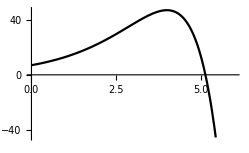

```mathematica
Plot[2^x 2^3 - 3^x,{x,0, 6},PlotStyle->Black]
```

### A compact Gersonides proof

```mathematica
Grid[{Range[20],Table[Mod[3^k,8],{k,1,20}]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1

### Herschfeld rules out 7s

```mathematica
Grid[{Range[20],Table[Mod[2^k,3],{k,1,20}]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1

```mathematica
Grid[{Range[20],Table[Mod[3^k,4],{k,1,20}]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1 | 3 | 1

### Herschfeld tackles 5

```mathematica
Grid[{Range[20],Table[Mod[3^k,64],{k,1,20}]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
3 | 9 | 27 | 17 | 51 | 25 | 11 | 33 | 35 | 41 | 59 | 49 | 19 | 57 | 43 | 1 | 3 | 9 | 27 | 17

```mathematica
Grid[{Range[20],Table[Mod[2^k,17],{k,1,20}]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
2 | 4 | 8 | 16 | 15 | 13 | 9 | 1 | 2 | 4 | 8 | 16 | 15 | 13 | 9 | 1 | 2 | 4 | 8 | 16

### Contours

```mathematica
Floor[1000000./Log[2,3]]
```

630929

### Diagonal of a square

```mathematica
41/29 > Sqrt[2]
```

False

```mathematica
SetPrecision[Sqrt[2.],20]
```

1.4142135623730951455

### Circumference of a circle

```mathematica
Sqrt[10.]
```

3.16228

```mathematica
Convergents[Sqrt[2],10]
```

{1,3/2,7/5,17/12,41/29,99/70,239/169,577/408,1393/985,3363/2378}

### Logarithms are irrational

```mathematica
2^Log[2,3.]
```

3.

```mathematica
SetPrecision[Log[2,3.],20]
```

1.5849625007211562977

```mathematica
SetPrecision[1/Log[2,3.],20]
```

0.63092975357145741899

### Rhin and Ellison

```mathematica
With[{k=1000000,x=630029},(0.00220823)*3^x / x^13.3]
```

2.75130598923689×10^300520

```mathematica
With[{k=1000000,x=630029},2.^k/E^(x/10)]
```

1.5270388238252×10^273668

```mathematica
With[{k=1000000,x=630029},2.^k-3^x]
```

9.9006562292959×10^301029

```mathematica
With[{k=1000000,x=630029},(2.^k-3^x)/((0.00220823)*3^x / x^13.3)]
```

3.5985296684655×10^509

A penny is 26.5mm across. If 2^k-3^x were the width of a penny, Rhin’s estimate would be 10^491 light years. Our galaxy is about 105,000 light years across

```mathematica
26.5 *10^509 / 1000000 / (9.46 * 10^12) / 3.26 / 10^9
```

8.59284815626662×10^481

```mathematica
E^0.1
```

1.10517

```mathematica
2/1.1
```

1.81818

```mathematica
Reality[p_]:=2^Ceiling[p Log[2,3]]-3^p
```

```mathematica
Baker[p_]:=With[{q=p Log[2,3.]},3^p 1.11 / q^2]
```

```mathematica
Trivial[p_]:=With[{q=p Log[2,3.]},1.]
```

```mathematica
Rhin[p_]:= 3^p 0.00220823 / p^13.3
```

```mathematica
Ellison[p_]:=With[{q=p Log[2,3.]},2.^q E^(-q/10.)]
```

```mathematica
Dirichlet[p_]:=With[{q=p Log[2,3.]},3^p 1.11 / q]
```

Baker:     2^q - 3^p > 3^p 1.11a / q^(b-1)               ~ O(3^p / p^c) with c unknown
Rhin:     2^q - 3^p > 3^p 0.00220823 / p^13.3      ~ O(3^p / p^13.3)
Ellison:  2^q - 3^p > 2^q e^(-q/10)                           ~ O(1.8^q), or O(2.56^p)
Dirichlet:    2^q - 3^p < 3^p 1.11 / q                         ~ O(3^p / p) infinitely often

Ellison is the worst asymptotically, but it is tighter than Rhin until p > 571.

```mathematica
Reduce[Ellison[p]>Rhin[p],{p},Reals]
```

General::munfl: Exp[-1257.35] is too small to represent as a normalized machine number; precision may be lost.

Reduce::ivar: 7933 is not a valid variable.

Reduce[False,{7933},ℝ]

```mathematica
minp=2; maxp=700;
```

```mathematica
RealityPlot=ListLinePlot[Table[{p,Log[10,Reality[p]]},{p,minp,maxp}],ScalingFunctions->{"Log10","Log10"},PlotStyle->Gray];
```

```mathematica
BakerPlot=Plot[Log10[Baker[p]],{p,minp,maxp},ScalingFunctions->{"Log10","Log10"},PlotStyle->Black];
```

```mathematica
RhinPlot=Plot[Log[10,Rhin[p]],{p,minp,maxp},ScalingFunctions->{"Log10","Log10"},PlotStyle->Black];
```

```mathematica
EllisonPlot=Plot[Log[10.,Ellison[p]],{p,minp,maxp},ScalingFunctions->{"Log10","Log10"},PlotStyle->Black];
```

```mathematica
DirichletPlot=Plot[Log[10,Dirichlet[p]],{p,minp,maxp},ScalingFunctions->{"Log10","Log10"},PlotStyle->Red];
```

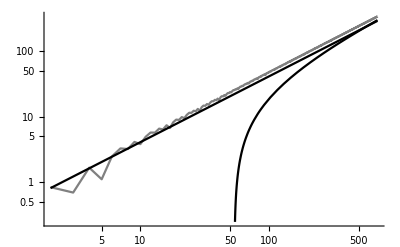

```mathematica
Show[RealityPlot,EllisonPlot,RhinPlot,PlotRange->All]
```

### 5n+1 circuits

```mathematica
Format[primeFactorForm[n_Integer]]:=CenterDot@@Superscript@@@FactorInteger[n]/. _[x_]:>x
```

```mathematica
Grid[Table[primeFactorForm[2^a 2^x-5^x],{x,1,4},{a,0,6}]]
```

(-1)^1·3^1 | (-1)^1 | 3^1 | 11^1 | 3^3 | 59^1 | 3^1·41^1
(-1)^1·3^1·7^1 | (-1)^1·17^1 | (-1)^1·3^2 | 7^1 | 3^1·13^1 | 103^1 | 3^1·7^1·11^1
(-1)^1·3^2·13^1 | (-1)^1·109^1 | (-1)^1·3^1·31^1 | (-1)^1·61^1 | 3^1 | 131^1 | 3^2·43^1
(-1)^1·3^1·7^1·29^1 | (-1)^1·593^1 | (-1)^1·3^1·11^1·17^1 | (-1)^1·7^1·71^1 | (-1)^1·3^2·41^1 | (-1)^1·113^1 | 3^1·7^1·19^1

### Germain primes

```mathematica
Table[Mod[x^3,13],{x,1,12}]
```

{1,8,1,12,8,8,5,5,1,12,5,12}

```mathematica
Table[Mod[x^3,7],{x,1,12}]
```

{1,1,6,1,6,6,0,1,1,6,1,6}

## Chapter 11. Let’s take a census

### Empirical counts of height-h numbers

Height of any odd number:

```mathematica
T[n_]:=If[EvenQ[n],n/2,3n+1]
```

```mathematica
v[n_]:=If[EvenQ[n],v[n/2],n]
```

```mathematica
u[n_]:=If[EvenQ[n],v[n],v[3n+1]]
```

```mathematica
h[n_]:=If[n==1,0,1+h[u[n]]]
```

```mathematica
h[27]
```

41

Compile the list of heights for first 2^19 odd numbers. This takes a while.

```mathematica
heights=Prepend[Table[{2n+1,h[2n+1]},{n,1,2^18}],{1,0}];
```

Extract numbers of height h less than or equal to x:

```mathematica
pihx[h_,x_]:=Map[If[#[[2]]==h && #[[1]]<=x,#[[1]],Nothing]&,heights]
```

```mathematica
pihx[1,2^18]
```

{5,21,85,341,1365,5461,21845,87381}

Less than x = 1000

```mathematica
pihx12=Table[{h,pihx[h,1000]},{h,1,100}];
```

```mathematica
Length[Sort[Flatten[Map[#[[2]]&,pihx12]]]]
```

499

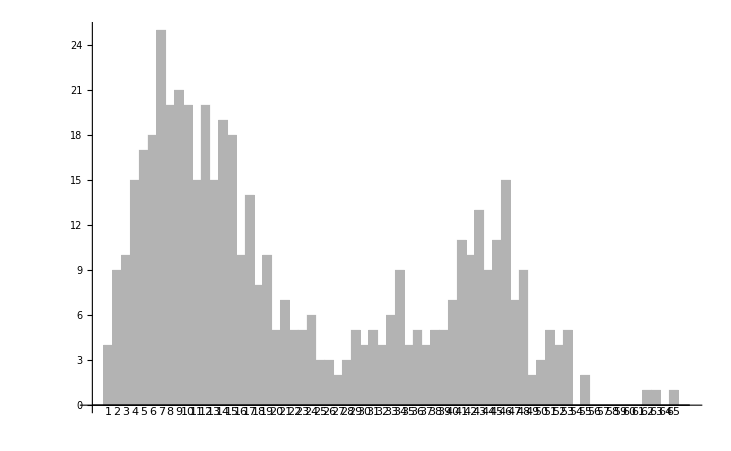

```mathematica
BarChart[Map[Length[#[[2]]]&,Take[pihx12,65]],ChartLabels->Range[65],PlotTheme->"GrayColor",BaseStyle->Directive[FontSize->8]]
```

Less than x = 10^6

```mathematica
pihx18=Table[{h,pihx[h,10^6]},{h,1,150}];
```

Missing one! Must have a huge height.

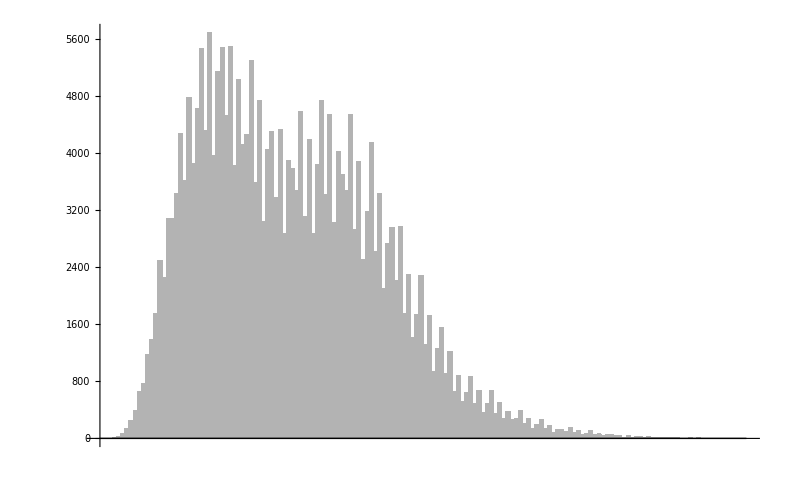

```mathematica
BarChart[Map[Length[#[[2]]]&,Take[pihx18,150]],PlotTheme->"GrayColor"]
```

### Height-2 numbers

Let’s calculate how many height-2 numbers there are, by drawing a chart (separate).

There are two types.
	(a) Ones that satisfy: 3((3x+1)/(2^(2m-1)))+1 = 2^(6n-2)   		odd -> even* -> odd -> 2^n
	(b) And ones that satisfy: 3((3x+1)/(2^(2m)))+1 = 2^(6n+2)		odd -> even* -> odd -> 2^n

For (a):
	((2^(6n-2)-1)/3) * 2^(2m-1) - 1
	---------------------------------------  = x
          		                 3

Change the "=" to "<=", and simplify:
	 (2^(6n-2)-1) * 2^(2m-1) <= 9x + 3

If we ignore the first "-1" and the last "3", we can take the log of both sides and look for solutions in positive integer (n,m) combinations.

#### Less than x = 2^12

```mathematica
Length[Solve[6n-2+2m-1<=Log[2,2^12*9],{n,m},PositiveIntegers]]
```

9

```mathematica
Length[Solve[6n+2+2m<=Log[2,2^12*9],{n,m},PositiveIntegers]]
```

3

```mathematica
Length[pihx[2,2^12]]
```

12

#### Less than x = 2^18

```mathematica
Length[Solve[6n-2+2m-1<=Log[2,2^18*9],{n,m},PositiveIntegers]]
```

18

```mathematica
Length[Solve[6n+2+2m<=Log[2,2^18*9],{n,m},PositiveIntegers]]
```

9

```mathematica
Length[pihx[2,2^18]]
```

27

```mathematica
methodSolveH2[x_]:=Length[Solve[2^(6n-2)2^(2m-1)<= 9x + 3,{n,m},PositiveIntegers]]+Length[Solve[2^(6n+2) 2^(2m)<= 9x + 3,{n,m},PositiveIntegers]]
```

```mathematica
Grid[Transpose[Prepend[Table[With[{x=2^(6y)},{StringJoin["2^",ToString[6y]],If[y>3,"unk",Length[pihx[2,x]]],methodSolveH2[x]}],{y,1,8}],{"x","Actual","Solve"}]]]
```

x | 2^6 | 2^12 | 2^18 | 2^24 | 2^30 | 2^36 | 2^42 | 2^48
Actual | 3 | 12 | 27 | unk | unk | unk | unk | unk
Solve | 3 | 12 | 27 | 48 | 75 | 108 | 147 | 192

### Height-3 numbers

18n-14 over, 1 up, 6m-3 over, 1 up, 2p over
18n-14 over, 1 up, 6m-1 over, 1 up, 2p-1 over
18n-8 over, 1 up, 6m-5 over, 1 up, 2p-1 over
18n-8 over, 1 up, 6m-1 over, 1 up, 2p over
18n-2 over, 1 up, 6m-5 over, 1 up, 2p over
18n-2 over, 1 up, 6m-3 over, 1 up, 2p-1 over
18n-10 over, 1 up, 6m-4 over, 1 up, 2p-1 over
18n-10 over, 1 up, 6m over, 1 up, 2p over
18n-4 over, 1 up, 6m-2 over, 1 up, 2p over
18n-4 over, 1 up, 6m over, 1 up, 2p-1 over
18n+2 over, 1 up, 6m-4 over, 1 up, 2p over
18n+2 over, 1 up, 6m-2 over, 1 up, 2p-1 over

Random testing

```mathematica
height3sample[path_,n_,m_,p_]:=If[path==1,(((2^(18n-14)-1)/3 2^(6m-3)-1)/3 *2^(2p)-1)/3,
If[path==9,(((2^(18n-4)-1)/3 2^(6m-2)-1)/3 *2^(2p)-1)/3,
If[path==10,(((2^(18n-4)-1)/3 2^(6m)-1)/3 *2^(2p-1)-1)/3,
If[path==11,(((2^(18n+2)-1)/3 2^(6m-4)-1)/3 *2^(2p)-1)/3,
If[path==12,(((2^(18n+2)-1)/3 2^(6m-2)-1)/3 *2^(2p-1)-1)/3, Nothing]]]]]
```

```mathematica
height3sample[1,2,2,2]
```

1272582597

```mathematica
h[1272582597]
```

3

```mathematica
methodSolveH3[x_]:=Length[Solve[2^(18n-14)2^(6m-3)2^(2p)<=27*x+12 ,{n,m,p},PositiveIntegers]]+Length[Solve[2^(18n-14)2^(6m-1)2^(2p-1)<=27*x+12 ,{n,m,p},PositiveIntegers]]+ Length[Solve[2^(18n-8)2^(6m-5)2^(2p-1)<=27*x+12 ,{n,m,p},PositiveIntegers]]+Length[Solve[2^(18n-8)2^(6m-1)2^(2p)<=27*x+12 ,{n,m,p},PositiveIntegers]]+Length[Solve[2^(18n-2)2^(6m-5)2^(2p)<=27*x+12 ,{n,m,p},PositiveIntegers]]+Length[Solve[2^(18n-2)2^(6m-3)2^(2p-1)<=27*x+12 ,{n,m,p},PositiveIntegers]]+Length[Solve[2^(18n-10)2^(6m-4)2^(2p-1)<=27*x+12 ,{n,m,p},PositiveIntegers]]+Length[Solve[2^(18n-10)2^(6m)2^(2p)<=27*x+12 ,{n,m,p},PositiveIntegers]]+Length[Solve[2^(18n-4)2^(6m-2)2^(2p)<=27*x+12 ,{n,m,p},PositiveIntegers]]+Length[Solve[2^(18n-4)2^(6m)2^(2p-1)<=27*x+12 ,{n,m,p},PositiveIntegers]]+Length[Solve[2^(18n+2)2^(6m-4)2^(2p)<=27*x+12 ,{n,m,p},PositiveIntegers]]+Length[Solve[2^(18n+2)2^(6m-2)2^(2p-1)<=27*x+12 ,{n,m,p},PositiveIntegers]]
```

```mathematica
methodSolveH3[64]
```

Solve::ivar: 7933 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

36

```mathematica
Grid[Transpose[Prepend[Table[With[{x=2^(6y)},{StringJoin["2^",ToString[6y]],If[y>3,"unk",Length[pihx[3,x]]],methodSolveH3[x]}],{y,1,8}],{"x","Actual","Solve"}]]]
```

Solve::ivar: 7933 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

x | 2^6 | 2^12 | 2^18 | 2^24 | 2^30 | 2^36 | 2^42 | 2^48
Actual | 2 | 17 | 57 | unk | unk | unk | unk | unk
Solve | 36 | 36 | 36 | 36 | 36 | 36 | 36 | 36

### Counting solutions of Diophantine inequalities

Example:  2x + 3y <= 20.

Bogan-Dov’s 1972 bound on positive integer solutions to linear Diophantine inequality, using the “pyramid” method, also re-invented by myself.

```mathematica
boganDov[coeff_,n_]:=With[{h=Length[coeff]},(n - Total[coeff])^h / (h! Apply[Times,coeff])]
```

Bound gives lower bound of 18.75 positive integer solutions for this inequality, when there are actually 27.

```mathematica
{boganDov[{2,3},20.],Length[Solve[2n+3m<=20,{n,m},PositiveIntegers]]}
```

{18.75,27}

The bound is bad when the number of solutions is small, but good when larger. Note that if n < Total[coeff], then it predicts a negative number of solutions, but more usefully, it identifies that there are no solutions in reality.

Here are undercounted solutions for height-3 numbers, compared with accurate counts.

```mathematica
Table[{k,boganDov[{18,6,2.},k],Length[Solve[18p+6n+2m<=k,{n,m,p},PositiveIntegers]]},{k,1,50}]
```

Solve::ivar: 7933 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

{{1,-12.0563,3},{2,-10.6667,3},{3,-9.38812,3},{4,-8.21605,3},{5,-7.14583,3},{6,-6.17284,3},{7,-5.29244,3},{8,-4.5,3},{9,-3.7909,3},{10,-3.16049,3},{11,-2.60417,3},{12,-2.11728,3},{13,-1.69522,3},{14,-1.33333,3},{15,-1.02701,3},{16,-0.771605,3},{17,-0.5625,3},{18,-0.395062,3},{19,-0.26466,3},{20,-0.166667,3},{21,-0.0964506,3},{22,-0.0493827,3},{23,-0.0208333,3},{24,-0.00617284,3},{25,-0.000771605,3},{26,0.,3},{27,0.000771605,3},{28,0.00617284,3},{29,0.0208333,3},{30,0.0493827,3},{31,0.0964506,3},{32,0.166667,3},{33,0.26466,3},{34,0.395062,3},{35,0.5625,3},{36,0.771605,3},{37,1.02701,3},{38,1.33333,3},{39,1.69522,3},{40,2.11728,3},{41,2.60417,3},{42,3.16049,3},{43,3.7909,3},{44,4.5,3},{45,5.29244,3},{46,6.17284,3},{47,7.14583,3},{48,8.21605,3},{49,9.38812,3},{50,10.6667,3}}

### Undercounting lattice points

Using the bound of Bogan-Dov.

```mathematica
methodAreaH2[x_]:=boganDov[{6,2},Log[2,x]+2 Log[2,3]+3] + boganDov[{6,2},Log[2,x]+2 Log[2,3]-2]
```

```mathematica
methodAreaH3[x_]:=boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+17]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+16]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+14]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+9]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+7]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+6]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+15]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+12]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+6]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+5]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+2]+boganDov[{18,6,2},Log[2,x]+3 Log[2,3]+-1]
```

### Closed form for infinite sums

### n^k / k!

```mathematica
Sum[n^k/k!,{k,0,Infinity}]
```

ⅇ^n

```mathematica
Sum[n^k/k!,{k,0,z}]
```

(ⅇ^n Gamma[1+z,n])/(z!)

```mathematica
With[{n=2000},{n,E^n/2.,Sum[1.*n^k/k!,{k, 0, n}]}]
```

{2000,1.94059009714218×10^868,1.96367031315699×10^868}

### (n-k)^k / k!

```mathematica
Sum[(n-k)^k/k!,{k, 0, Infinity}]
```

Sum::div: Sum does not converge.

∑_(k=0)^∞ (-k+n)^k/(k!)

```mathematica
Sum[(n-k)^k/k!,{k,0, n}]
```

∑_(k=0)^n (-k+n)^k/(k!)

```mathematica
With[{n=10},Table[1.*(n-k)^k/k!,{k, 0, 10}]]
```

{1.,9.,32.,57.1667,54.,26.0417,5.68889,0.433929,0.00634921,2.75573×10^-6,0.}

```mathematica
Total[With[{n=10},Table[1.*(n-k)^k/k!,{k, 0, 10}]]]
```

185.338

@Gary from mathstackexchange worked out the closed form: (1 / (1+omega)) e^(omega n).

```mathematica
omega=ProductLog[1.]
```

0.567143

```mathematica
ClosedForm1[n_]:=(1./(1+omega)) E^(omega n)
```

```mathematica
(1./(1+omega))
```

0.638104

### Undercounting census teams

Instructions:
	Move to the right 6n
	Go up
	Move to the right 6m
	Go up
	etc.

```mathematica
methodOneteam1[x_,h_]:=(Log[2,x]/6-h)^h / h!
```

```mathematica
methodOneteam2[x_,h_]:=(Log[2,x]+h Log[2,3]-6h)^h / (6^h * h!)
```

```mathematica
methodOneteam3[x_,h_]:=2(Log[2,x]+h Log[2,3]-6h)^h / (6^h * h!)
```

```mathematica
teamsInGroup[h_,i_]:=Binomial[h,i]-Binomial[h-2,i-1]
```

```mathematica
methodOneteam4[x_,h_]:=Sum[teamsInGroup[h,i]*(Log[2,x]+h Log[2,3]-6h)^h / (6^h * h!),{i,0,h+1}]
```

```mathematica
methodOneteam5[x_,h_]:=Sum[teamsInGroup[h,i]*(Log[2,x]+h Log[2,3]+2i-6h)^h / (6^h * h!),{i,0,h+1}]
```

Applying the infinite sum to methodOneteam1 gives O(x^0.13).

```mathematica
exponent=omega *Log[2,E]/6.
```

0.136369

Getting rid of the multiplicative constant.

```mathematica
Reduce[(1/(1+omega))x^exponent > x^0.13,{x},Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x>4.3×10^30

```mathematica
Reduce[(1/(1+omega))x^exponent > x^0.1,{x},Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

x>231568.

```mathematica
(10^1000)^0.13
```

1.×10^130

x^0.13 is approximately sqrt(sqrt(sqrt(x))).

```mathematica
Table[With[{x=2^(6y)},{6y,(1./(1+omega))x^exponent}],{y,1,30}]
```

{{6,1.12512},{12,1.98384},{18,3.49794},{24,6.16766},{30,10.875},{36,19.175},{42,33.8097},{48,59.6141},{54,105.113},{60,185.338},{66,326.791},{72,576.206},{78,1015.98},{84,1791.4},{90,3158.63},{96,5569.38},{102,9820.05},{108,17314.9},{114,30530.1},{120,53831.4},{126,94916.7},{132,167359.},{138,295092.},{144,520312.},{150,917427.},{156,1.61763×10^6},{162,2.85224×10^6},{168,5.02913×10^6},{174,8.86748×10^6},{180,1.56353×10^7}}

### Height 2 with one census team: sample numbers found

```mathematica
Table[{n,m,((4*2^(6n)-1)/3*2^(6m)-1)/3},{m,1,5},{n,1,5}]
```

{{{1,1,1813},{2,1,116501},{3,1,7456533},{4,1,477218581},{5,1,30541989653}},{{1,2,116053},{2,2,7456085},{3,2,477218133},{4,2,30541989205},{5,2,1954687337813}},{{1,3,7427413},{2,3,477189461},{3,3,30541960533},{4,3,1954687309141},{5,3,125099989620053}},{{1,4,475354453},{2,4,30540125525},{3,4,1954685474133},{4,4,125099987785045},{5,4,8006399335683413}},{{1,5,30422685013},{2,5,1954568033621},{3,5,125099870344533},{4,5,8006399218242901},{5,5,512409557483738453}}}

### Height 3 with one census team: sample numbers found (not always whole numbers)

```mathematica
Table[{n,m,p,(((4*2^(6n)-1)/3*2^(6m)-1)/3*2^(6p)-1)/3},{p,1,2},{m,1,2},{n,1,2}]
```

{{{{1,1,1,38677},{2,1,1,7456063/3}},{{1,2,1,2475797},{2,2,1,477189439/3}}},{{{1,1,2,2475349},{2,1,2,477188095/3}},{{1,2,2,158451029},{2,2,2,30540124159/3}}}}

### Undercounting results

### h=2

```mathematica
Grid[Transpose[Prepend[Table[With[{x=2^(6y)},{StringJoin["2^",ToString[6y]],If[y>3,"unk",Length[pihx[2,x]]],methodSolveH2[x*1.],methodAreaH2[x*1.],methodOneteam1[x*1.,2],methodOneteam2[x*1.,2],methodOneteam3[x*1.,2],methodOneteam4[x*1.,2],methodOneteam5[x*1.,2]}],{y,1,15}],{"x","Actual","Solver","Area","Oneteam1","Oneteam2","Oneteam3","Oneteam4","Oneteam5"}]]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

x | 2^6 | 2^12 | 2^18 | 2^24 | 2^30 | 2^36 | 2^42 | 2^48 | 2^54 | 2^60 | 2^66 | 2^72 | 2^78 | 2^84 | 2^90
Actual | 3 | 12 | 27 | unk | unk | unk | unk | unk | unk | unk | unk | unk | unk | unk | unk
Solver | 3 | 12 | 27 | 48 | 75 | 108 | 147 | 192 | 243 | 300 | 363 | 432 | 507 | 588 | 675
Area | 0.753221 | 5.42315 | 16.0931 | 32.763 | 55.4329 | 84.1028 | 118.773 | 159.443 | 206.113 | 258.783 | 317.452 | 382.122 | 452.792 | 529.462 | 612.132
Oneteam1 | 0.5 | 0. | 0.5 | 2. | 4.5 | 8. | 12.5 | 18. | 24.5 | 32. | 40.5 | 50. | 60.5 | 72. | 84.5
Oneteam2 | 0.111241 | 0.139561 | 1.16788 | 3.1962 | 6.22452 | 10.2528 | 15.2812 | 21.3095 | 28.3378 | 36.3661 | 45.3944 | 55.4228 | 66.4511 | 78.4794 | 91.5077
Oneteam3 | 0.222481 | 0.279123 | 2.33576 | 6.39241 | 12.449 | 20.5057 | 30.5623 | 42.619 | 56.6756 | 72.7323 | 90.7889 | 110.846 | 132.902 | 156.959 | 183.015
Oneteam4 | 0.333722 | 0.418684 | 3.50365 | 9.58861 | 18.6736 | 30.7585 | 45.8435 | 63.9285 | 85.0134 | 109.098 | 136.183 | 166.268 | 199.353 | 235.438 | 274.523
Oneteam5 | 0.13982 | 1.22478 | 5.30975 | 12.3947 | 22.4797 | 35.5646 | 51.6496 | 70.7346 | 92.8195 | 117.904 | 145.989 | 177.074 | 211.159 | 248.244 | 288.329

### h=3

```mathematica
Grid[Transpose[Prepend[Table[With[{x=2^(6y)},{StringJoin["2^",ToString[6y]],If[y>3,"unk",Length[pihx[3,x]]],methodSolveH3[x*1.],methodAreaH3[x*1.],methodOneteam1[x*1.,3],methodOneteam2[x*1.,3],methodOneteam3[x*1.,3],methodOneteam4[x*1.,3],methodOneteam5[x*1.,3]}],{y,1,15}],{"x","Actual","Solver","Area","Oneteam1","Oneteam2","Oneteam3","Oneteam4","Oneteam5"}]]]
```

Solve::ivar: 7933 is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

x | 2^6 | 2^12 | 2^18 | 2^24 | 2^30 | 2^36 | 2^42 | 2^48 | 2^54 | 2^60 | 2^66 | 2^72 | 2^78 | 2^84 | 2^90
Actual | 2 | 17 | 57 | unk | unk | unk | unk | unk | unk | unk | unk | unk | unk | unk | unk
Solver | 36 | 36 | 36 | 36 | 36 | 36 | 36 | 36 | 36 | 36 | 36 | 36 | 36 | 36 | 36
Area | -7.7939 | -0.399885 | 6.5039 | 24.9175 | 66.8408 | 144.274 | 269.217 | 453.669 | 709.632 | 1049.1 | 1484.09 | 2026.58 | 2688.58 | 3482.09 | 4419.11
Oneteam1 | -1.33333 | -0.166667 | 0. | 0.166667 | 1.33333 | 4.5 | 10.6667 | 20.8333 | 36. | 57.1667 | 85.3333 | 121.5 | 166.667 | 221.833 | 288.
Oneteam2 | -0.293447 | -0.00148943 | 0.0829499 | 0.95987 | 3.62927 | 9.09116 | 18.3455 | 32.3924 | 52.2317 | 78.8635 | 113.288 | 156.505 | 209.514 | 273.316 | 348.91
Oneteam3 | -0.586895 | -0.00297886 | 0.1659 | 1.91974 | 7.25854 | 18.1823 | 36.691 | 64.7847 | 104.463 | 157.727 | 226.576 | 313.009 | 419.028 | 546.631 | 697.82
Oneteam4 | -1.76068 | -0.00893659 | 0.497699 | 5.75922 | 21.7756 | 54.5469 | 110.073 | 194.354 | 313.39 | 473.181 | 679.727 | 939.027 | 1257.08 | 1639.89 | 2093.46
Oneteam5 | -0.570358 | 0.11439 | 2.55402 | 12.7485 | 36.698 | 80.4023 | 149.861 | 251.076 | 390.044 | 572.768 | 805.247 | 1093.48 | 1443.47 | 1861.21 | 2352.71

### Histogram of predicted versus actual counts

It seems impossible to make a single plot, because x^0.13 is too small to see.
Here the true heights are for x = 2^18, but the predicted heights for x = 2^90.

### x = 2^18

```mathematica
real18=Table[Length[pihx[h,2^18]],{h,1,150}];
```

```mathematica
guessed18=Table[If[h>3,0,methodOneteam1[2^18.,h]],{h, 1, 150}];
```

```mathematica
guessed90=Table[If[h>15,0,methodOneteam1[2^90.,h]],{h, 1, 150}];
```

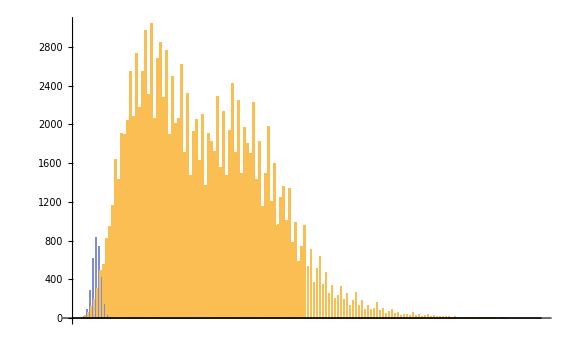

```mathematica
BarChart[MapThread[{#1,#2}&,{real18,guessed90}]]
```

```mathematica
guessed90=Table[If[h>5,0,methodOneteam5[2^30.,h]],{h, 1, 150}];
```

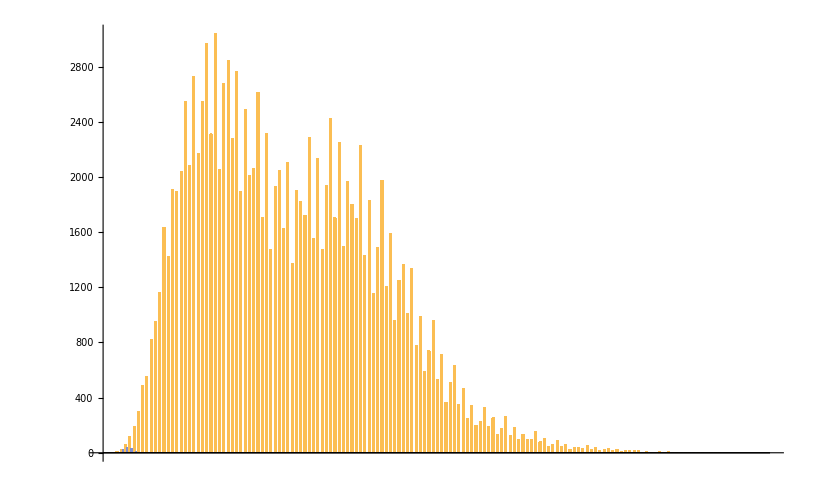

```mathematica
BarChart[MapThread[{#1,#2}&,{real18,guessed90}]]
```

### Chaos radiates from the number 1

```mathematica
CollatzTree1[n_,cutoff_,height_,depth_]:=
If[(depth==1)||(n>cutoff),n,
If[2n>cutoff,
If[(n>4)&&EvenQ[n]&&(Mod[n,3]==1),
n[CollatzTree1[(n-1)/3,cutoff,If[OddQ[n],height+1,height],depth-1]],n],
If[(n>4)&&EvenQ[n]&&(Mod[n,3]==1),
n[CollatzTree1[(n-1)/3,cutoff,If[OddQ[n],height+1,height],depth-1],
CollatzTree1[2n,cutoff,If[OddQ[n],height+1,height],depth-1]],
n[CollatzTree1[2n,cutoff,If[OddQ[n],height+1,height],depth-1]]]]]
```

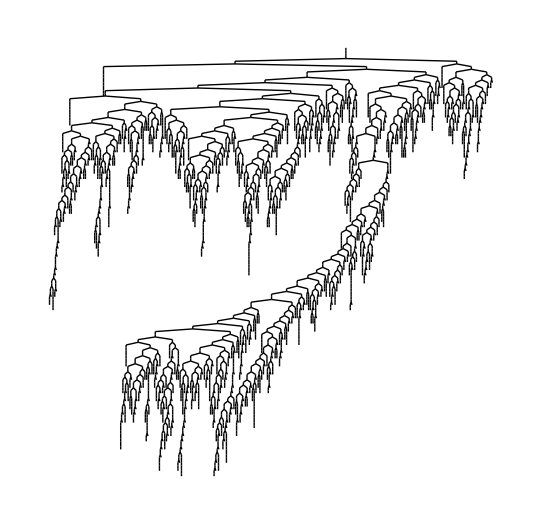

```mathematica
TreeForm[CollatzTree1[1,10000,0,1000],VertexLabeling->Automatic,VertexRenderingFunction->None,EdgeRenderingFunction->({Black,Line[#]}&)]
```

### Notes and references

```mathematica
state1=19000; state2=17000;state3=6000;
```

```mathematica
apportion[seats_]:=With[{totalpop=state1+state2+state3},{1.*seats*state1/totalpop,1.*seats*state2/totalpop,1.*seats*state3/totalpop}]
```

```mathematica
Grid[Table[{i,apportion[i]},{i,45,46}]]
```

45 | {20.3571,18.2143,6.42857}
46 | {20.8095,18.619,6.57143}

## Chapter 12. If there’s a cycle, it’s long

### Relating cycle lengths with member sizes

```mathematica
(3^8-2^8)/(2^13-3^8)*1.
```

3.86573

```mathematica
A[n_]:=(3n+1)/2
```

```mathematica
B[n_]:=n/2
```

```mathematica
B[B[B[B[B[A[A[A[A[A[A[A[A[(3^8-2^8)/(2^13-3^8)*1.]]]]]]]]]]]]]
```

3.86573

```mathematica
A[A[A[A[A[A[A[A[(3^8-2^8)/(2^13-3^8)*1.]]]]]]]]
```

123.703

```mathematica
B[A[B[A[A[B[A[B[A[A[B[A[A[8.8909]]]]]]]]]]]]]
```

8.89089

### A formula for the bottom member of the high cycle

```mathematica
BetaAnd[l_,i_,x_]:=If[Last[Take[l]]==1,2^(i-1)*3^(x-Count[l,1]),0]
```

```mathematica
BetaValue[necklace_]:=1.*Total[Table[BetaAnd[Take[necklace,i],i,Count[necklace,1]],{i,1,Length[necklace]}]]
```

```mathematica
Rotations[l_]:=Table[RotateLeft[l,i],{i,1,Length[l]}]
```

```mathematica
InsertBetas[a_]:=Map[{BetaValue[#],#}&,a]
```

```mathematica
SelectMin[a_]:=First[MinimalBy[a,First]]
```

```mathematica
Stats[l_]:={Length[l],Length[Select[l,#==1&]]}
```

```mathematica
Rep[x_,n_]:=Flatten[Apply[Join,Table[{x},{m,1,n}]]]
```

```mathematica
CircuitLoop[x_,k_]:=Join[Rep[1,x],Rep[0,k-x]]
```

```mathematica
CircuitLoop[5,8]
```

{1,1,1,1,1,0,0,0}

```mathematica
AddOnes[x_,l_]:=With[{k=Length[l]},Table[Floor[(k/x)(i-1)+1.],{i,1,x}]]
```

```mathematica
HighLoop[x_,k_]:=With[{indices=AddOnes[x,Rep[0,k]]},Table[If[MemberQ[indices,i],1,0],{i,1,k}]]
```

```mathematica
HighLoop[5,8]
```

{1,1,0,1,1,0,1,0}

```mathematica
HighLoop[12,19]
```

{1,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0}

```mathematica
HighLoop[41,65]
```

{1,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0}

```mathematica
HighLoop[8,13]
```

{1,1,0,1,1,0,1,0,1,1,0,1,0}

```mathematica
BetaValue[HighLoop[8,13]]/(2^13-3^8)
```

8.89086

Example:  x=971, k=1539

```mathematica
BetaValue[CircuitLoop[971,1539]]/(2^1539-3^971.)
```

1021.3837

```mathematica
BetaValue[HighLoop[971,1539]]/(2^1539-3^971.)
```

238670.391

```mathematica
Table[(2.^(Ceiling[x*Log[2,3]]+1)-3^x)/(2.^Ceiling[x*Log[2,3]]-3^x),{x,80,100}]
```

{8.6186,3.86991,45.1209,4.74534,3.22099,6.70211,3.62102,14.8322,4.28708,3.09132,5.60301,3.42168,9.37484,3.94504,108.17,4.89108,3.25862,7.09299,3.6803,17.7677,4.39295}

While the numerator increases reliably by about 1.5 times:

```mathematica
Table[BetaValue[HighLoop[x, Ceiling[x*Log[2,3]]+1]]/BetaValue[HighLoop[x, Ceiling[x*Log[2,3]]]],{x,80,100}]
```

{1.54177,1.45042,1.44005,1.4459,1.48309,1.5226,1.47284,1.44027,1.43308,1.48234,1.55354,1.47063,1.4518,1.45437,1.4456,1.5582,1.46924,1.46237,1.45233,1.44538,1.56336}

Increasing k from “x log 3” to “x log 3 + 1” causes the altitude of the highest (x)-loop to decrease.

How does the altitude change as we increase k beyond x log 3?

Here's an example with k=32+, x= 20.

```mathematica
loop=HighLoop[20,32]
```

{1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0,1,1,0,1,1,0,1,0}

```mathematica
loop=HighLoop[20,100]
```

{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1,0,0,0,0}

Here is a log10 plot of altitude versus “extra k”.

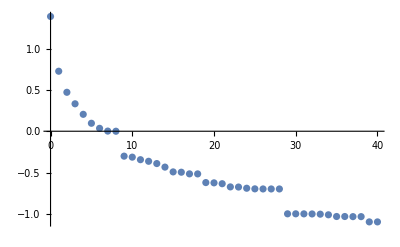

```mathematica
ListPlot[With[{k=32,x=20},Table[{i,Log[10,BetaValue[Join[HighLoop[x,k+i],Table[0,{j,1,i}]]]/(2^(k+i)-3^x)]},{i,0,40}]]]
```

When k=40, x=20, we just have a repetition of the trivial 1-2-1 loop, with altitude = 1.

```mathematica
HighLoop[20,40]
```

{1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0,1,0}

```mathematica
BetaValue[HighLoop[20,40]]/(2^40-3^20)    (* same as 1-2-1 loop *)
```

1.

All loops with x = 1 to 1000

```mathematica
MaximalBy[Table[With[{k=Ceiling[x* Log[2,3]]},{k,x,BetaValue[HighLoop[x,k]]/(2.^k-3.^x)}],{x,1,1000}],#[[3]]&]
```

{{1539,971,238670.390873}}

Because beta(k,x) for the constructed loop involves floors and ceilings, it is hard to work with.

So we compute an overestimate of beta(k,x), by getting rid of the floors when we distribute the (3n+1)/2 operations among the n/2 operations, and getting rid of the ceiling in selecting k.

```mathematica
Sum[2^(((5 * Log[2,3]+1)/5)*i) 3^(5-i-1),{i,0,4}]
```

81+27 2^(1/5 (1+(5 Log[3])/Log[2]))+9 2^(2/5 (1+(5 Log[3])/Log[2]))+3 2^(3/5 (1+(5 Log[3])/Log[2]))+2^(4/5 (1+(5 Log[3])/Log[2]))

```mathematica
Sum[2^(((5 * Log[2,3]+1)/5)*i) 3^(5.-i-1),{i,0,4}]
```

544.727

```mathematica
BetaOverestimate[x_]:=Sum[2^((x * Log[2,3] + 1.)/x*i) 3^(x-i-1),{i,0,x-1}]
```

```mathematica
BetaOverestimate[5]
```

544.727

How good is the upper bound for beta(k,x)?

```mathematica
Table[With[{ups=Prime[x]},With[{k=Ceiling[ups Log[2,3]]},{k,ups,BetaExact[ups], BetaOverestimate[ups]}]],{x,1,20}]
```

{{4,2,BetaExact[2],7.24264},{5,3,BetaExact[3],34.6259},{8,5,BetaExact[5],544.727},{12,7,BetaExact[7],7003.59},{18,11,BetaExact[11],907872.},{21,13,BetaExact[13],9.70384×10^6},{27,17,BetaExact[17],1.03438×10^9},{31,19,BetaExact[19],1.04271×10^10},{37,23,BetaExact[23],1.02567×10^12},{46,29,BetaExact[29],9.4573×10^14},{50,31,BetaExact[31],9.10562×10^15},{59,37,BetaExact[37],7.9372×10^18},{65,41,BetaExact[41],7.1307×10^20},{69,43,BetaExact[43],6.73334×10^21},{75,47,BetaExact[47],5.96546×10^23},{85,53,BetaExact[53],4.90809×10^26},{94,59,BetaExact[59],3.98571×10^29},{97,61,BetaExact[61],3.70945×10^30},{107,67,BetaExact[67],2.97169×10^33},{113,71,BetaExact[71],2.55152×10^35}}

This overestimate looks pretty tight.  As x increases, the estimate is somewhere between 1.4x and 2x too high:

```mathematica
Table[With[{ups=Prime[x]},With[{k=Ceiling[ups Log[2,3]]},{k,ups,BetaOverestimate[ups]/BetaExact[ups]}]],{x,80,100}]
```

{{649,409,(2.72899×10^197)/BetaExact[409]},{665,419,(1.65087×10^202)/BetaExact[419]},{668,421,(1.49288×10^203)/BetaExact[421]},{684,431,(9.02489×10^207)/BetaExact[431]},{687,433,(8.16013×10^208)/BetaExact[433]},{696,439,(6.03123×10^211)/BetaExact[439]},{703,443,(4.92984×10^213)/BetaExact[443]},{712,449,(3.64257×10^216)/BetaExact[449]},{725,457,(2.4325×10^220)/BetaExact[457]},{731,461,(1.98759×10^222)/BetaExact[461]},{734,463,(1.79659×10^223)/BetaExact[463]},{741,467,(1.46782×10^225)/BetaExact[467]},{760,479,(8.00121×10^230)/BetaExact[479]},{772,487,(5.33733×10^234)/BetaExact[487]},{779,491,(4.35877×10^236)/BetaExact[491]},{791,499,(2.90642×10^240)/BetaExact[499]},{798,503,(2.37308×10^242)/BetaExact[503]},{807,509,(1.75063×10^245)/BetaExact[509]},{826,521,(9.52304×10^250)/BetaExact[521]},{829,523,(8.60366×10^251)/BetaExact[523]},{858,541,(3.44803×10^260)/BetaExact[541]}}

Here’s a plot of actual log(beta), in blue dots, versus a solid-line upper bound.

```mathematica
maxc=200;betadotsplot=ListPlot[Table[With[{k=Ceiling[x Log[2,3]]},{x,Log[10,BetaValue[HighLoop[x,k]]]}],{x,180,maxc}],ScalingFunctions->{"Log10","Log10"}];
```

```mathematica
betaupperboundplot=Plot[Log[10,3^x*x/2. ],{x,1,maxc},ScalingFunctions->{"Log10","Log10"}];
```

```mathematica
betalowerboundplot=Plot[Log[10,3^x * x/6.],{x,1,maxc},ScalingFunctions->{"Log10","Log10"}];
```

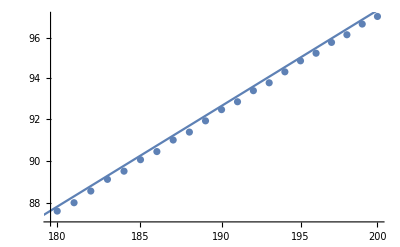

```mathematica
Show[betadotsplot,betaupperboundplot]
```

The looseness is the upper bound comes from “getting rid of the floors” being pessimistic.  For every big jump, there’s going to be a corresponding small jump somewhere else in the sum.

Upper bounding a particular loop’s altitude

We can use our overestimate for beta(k,x) in order to calculate an upper-bound the altitude of the (1539,971)-loop.

Our upper bound is ~476,000, compared to the loop’s actual altitude of ~238,000:

```mathematica
BetaOverestimate[971.]/(2^1539-3^971)
```

476767.251109896

```mathematica
BetaValue[HighLoop[971.,1539]]/(2^1539-3^971)
```

238670.390873132

```mathematica
aixtable=Table[Table[If[(x==0)&&(a==0),"x      a->",If[x==0,a,If[a==0,x,Sum[a^(i/x)*1.,{i,0,x-1}]/x]]],{a,{0,1.035,1.05,1.1,1.5,2.,2.0706,3.,3.864,4.}}],{x,{0,10.,100.,1000.,10000.,100000.,1000000.}}];
```

```mathematica
Grid[aixtable,Alignment->Left,Frame->All,ItemStyle->"Text"]
```

x      a-> | 1.035 | 1.05 | 1.1 | 1.5 | 2. | 2.0706 | 3. | 3.864 | 4.
10. | 1.01565 | 1.0223 | 1.04421 | 1.20832 | 1.39327 | 1.41805 | 1.72231 | 1.97883 | 2.01751
100. | 1.01722 | 1.02455 | 1.04871 | 1.23065 | 1.4377 | 1.46558 | 1.8105 | 2.10452 | 2.14908
1000. | 1.01738 | 1.02477 | 1.04916 | 1.2329 | 1.4422 | 1.4704 | 1.81948 | 2.11738 | 2.16254
10000. | 1.0174 | 1.02479 | 1.0492 | 1.23313 | 1.44265 | 1.47088 | 1.82038 | 2.11867 | 2.16389
100000. | 1.0174 | 1.0248 | 1.04921 | 1.23315 | 1.44269 | 1.47093 | 1.82047 | 2.11879 | 2.16403
1.×10^6 | 1.0174 | 1.0248 | 1.04921 | 1.23315 | 1.44269 | 1.47093 | 1.82048 | 2.11881 | 2.16404

Note that this sum can be re-written in closed form as  (a-1) / (xth root of a - 1).  I’m not sure if the closed-form is easier to compute, though.

```mathematica
Sum[a^(i/x),{i,0,x-1}]
```

-1773/(4624 (-1+(2851/4624)^(1/x)))

Fast, incremental computation of altitude bounds

In checking altitudes of highest-loops for x = 1 to 1,000,000, we have recomputed the highest loop (and its altitude) for each x:
   ...
   (3^12345 (12345/2)) / (2^ceiling(12345 log 3) - 3^12345
   (3^12346 (12346/2)) / (2^ceiling(12346 log 3) - 3^12346
   ...

However, given 3^x, we can quickly, incrementally, compute 3^(x+1) = 3^x * 3.
Given x/2, we can quickly compute (x+1)/2 = x/2 + 1/2.
Given x log 3, we can quickly compute (x+1) log 3 = x log 3 + log 3.

We can also keep track of the best altitude so far.  Here’s a 6-tuple state that we can incrementally update:

{ x , 3^x , x/2 , xlog3 , (3^x * x/2) / (2^k-3^x) , highest-altitudes-so-far }

```mathematica
Updater[state_]:=With[{s1=state[[1]]+1,s2=state[[2]]*3,s3=state[[3]]+1/2,s4=state[[4]]+Log[2,3]},With[{s5=(s2*s3)/(2.^Ceiling[s4]-s2)},{s1,s2,s3,s4,s5,If[s5>state[[6]][[1]][[2]],Insert[state[[6]],{s1,s5},1],state[[6]]]}]]
```

Confirmation

Let’s confirm that the incremental version gives the same results as the non-incremental version, at least for x=1 to 100,000.

```mathematica
BetaOverestimateClosed[x_]:=(x/2) 3.^x
```

```mathematica
MaximalBy[Table[With[{k=Ceiling[x* Log[2,3]]},{k,x,BetaOverestimateClosed[x]/(2^k-3^x)}],{x,1,100000}],#[[3]]&];
```

```mathematica
First[Nest[Updater,{1,3,1/2,Log[2,3],1,{{1,1}}},100000-1][[6]]]
```

{79335,1.082413391×10^10}

Empirical detection of high-altitude loops

Let’s start with x = 1 to 100.

```mathematica
res100=Map[{#[[1]],#[[5]]}&,NestList[Updater,{1,3,1/2,Log[2,3],1,{{1,1}}},99]]
```

{{1,1},{2,1.28571},{3,8.1},{4,3.44681},{5,46.7308},{6,7.41356},{7,4.00969},{8,16.0907},{9,6.76909},{10,45.5133},{11,11.4629},{12,6.16598},{13,20.6096},{14,9.28567},{15,44.3176},{16,14.3118},{17,216.185},{18,23.3307},{19,11.2071},{20,43.1435},{21,16.3455},{22,115.888},{23,25.0058},{24,12.678},{25,41.991},{26,17.8023},{27,87.9504},{28,26.0226},{29,572.457},{30,40.8601},{31,18.8379},{32,74.3476},{33,26.6012},{34,212.017},{35,39.7508},{36,19.5583},{37,66.0205},{38,26.8758},{39,141.335},{40,38.6628},{41,1778.15},{42,60.2228},{43,26.9331},{44,110.637},{45,37.5962},{46,350.377},{47,55.8383},{48,26.8313},{49,93.1612},{50,36.5508},{51,207.903},{52,52.3275},{53,26.611},{54,81.6815},{55,35.5265},{56,153.246},{57,49.3976},{58,565.298},{59,73.4317},{60,34.5233},{61,123.991},{62,46.8764},{63,292.907},{64,67.1248},{65,33.5409},{66,105.552},{67,44.6553},{68,203.844},{69,62.081},{70,942.119},{71,92.7215},{72,42.663},{73,159.239},{74,57.9072},{75,404.812},{76,83.1787},{77,40.8504},{78,132.214},{79,54.3602},{80,264.744},{81,75.7312},{82,1767.96},{83,113.931},{84,51.2817},{85,199.84},{86,69.7041},{87,558.199},{88,100.631},{89,48.5639},{90,162.135},{91,64.6863},{92,339.243},{93,90.4444},{94,4989.99},{95,137.326},{96,60.4137},{97,247.01},{98,82.3348},{99,780.503},{100,119.647}}

For each x, we plot the altitude of the highest (x)-loop.

We can see that for loops up to length (x=100, k=159), every loop has a member lower than 5000.  So there are no integer loops shorter than x=5000.

```mathematica
bar100plot=BarChart[Map[#[[2]]&,res100],ChartLabels->Table[If[Mod[i,5]==0,i, ],{i,1,100}],PlotTheme->"GrayColor"];
```

```mathematica
step100=Nest[Updater,{1,3,1/2,Log[2,3],1,{{1,1}}},100-1][[6]]
```

{{94,4989.99},{41,1778.15},{29,572.457},{17,216.185},{5,46.7308},{3,8.1},{2,1.28571},{1,1}}

```mathematica
step100plot=ListStepPlot[step100,Left,PlotRange->{{0,100},{0,5200}},PlotTheme->"GrayColor"];b=1
```

1

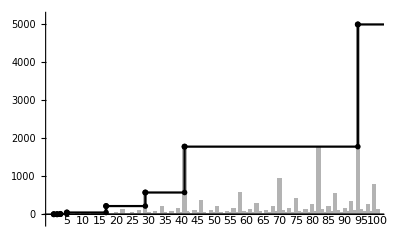

```mathematica
Show[bar100plot,step100plot,PlotRange->{{0,100},{-200,5200}}]
```

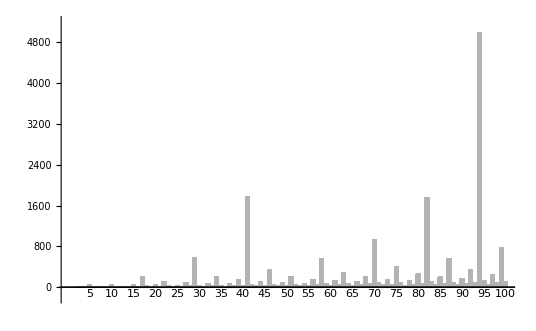

```mathematica
Show[bar100plot,PlotRange->{{0,100},{-200,5200}}]
```

```mathematica
(* Nest[Updater,{1,3,1/2,Log[2,3],1,{{1,1}}},10000000-1][[6]] *)
```

```mathematica
(* ListStepPlot[Insert[res10m,{10000000,res10m[[1]][[2]]},1],Left,ScalingFunctions->{"Log10","Log10"}] *)
```

```mathematica
(* res100m=Nest[Updater,{1,3,1/2,Log[2,3],1,{{1,1}}},100000000-1][[6]] *)
```

```mathematica
(* ListStepPlot[Insert[res100m,{100000000,res100m[[1]][[2]]},1],ScalingFunctions->{"Log","Log"}] *)
```

### The plot continues

```mathematica
maxb=100000
```

100000

As we increase x, let’s write down each loop that establishes a new “record” for altitude.

```mathematica
res=Nest[Updater,{1,3,1/2,Log[2,3],1,{{1,1}}},maxb-1][[6]]
```

{{79335,1.082413391×10^10},{47468,2.171511483×10^9},{15601,4.2872247934×10^8},{14936,1.2074254083×10^8},{14271,6.7629702276×10^7},{13606,4.56062826259×10^7},{12941,3.35555294934×10^7},{12276,2.5954245446×10^7},{11611,2.07221991433×10^7},{10946,1.69010631384×10^7},{10281,1.39879460681×10^7},{9616,1.16935713458×10^7},{8951,9.83974328128×10^6},{8286,8.31069903719×10^6},{7621,7.02796813257×10^6},{6956,5.93647479772×10^6},{6291,4.99642427081×10^6},{5626,4.17834683495×10^6},{4961,3.45995315802×10^6},{4296,2.82407295276×10^6},{3631,2.25726520015×10^6},{2966,1.74885782888×10^6},{2301,1.29026960984×10^6},{1636,874522.024522},{971,495881.785085},{306,149595.},{253,40607.2},{200,19186.3},{147,10050.3},{94,4989.99},{41,1778.15},{29,572.457},{17,216.185},{5,46.7308},{3,8.1},{2,1.28571},{1,1}}

Conclusion so far: no loop with x < 100,000 has a bottom member whose value exceeds 1.1 * 10^10.

So any integer loop has to have at least 100,000 odd terms.

```mathematica
resplot=ListStepPlot[res,Left,ScalingFunctions->{"Log10","Log10"}];
```

```mathematica
resdots=Map[{#[[1]],#[[5]]}&,NestList[Updater,{1,3,1/2,Log[2,3],1,{{1,1}}},maxb-1]];
resdotsplot=ListPlot[resdots,ScalingFunctions->{"Log10","Log10"}];
```

```mathematica
diophantineplot=Plot[0.71 x^2 ,{x,1,maxb},ScalingFunctions->{"Log10","Log10"}];
```

```mathematica
bakerplot=Plot[(x/2) 1.11 (x Log[2,3])^2,{x,1,maxb},ScalingFunctions->{"Log10","Log10"}];
```

```mathematica
rhinplot=Plot[(x/2) x^13.3 / 0.00220823 ,{x,1,maxb},ScalingFunctions->{"Log10","Log10"}];
```

```mathematica
lowerboundplot=Plot[x/3.,{x,1,maxb},ScalingFunctions->{"Log10","Log10"}];
```

```mathematica
circuit = Table[(3^x-2^x)/(2.^Ceiling[x Log[2,3]]-3^x),{x,1,maxb}];
circuitplot=ListPlot[circuit,ScalingFunctions->{"Log10","Log10"},PlotStyle->Orange];
```

```mathematica
ellisonplot=Plot[(x/2) 1.17^x,{x,1,1000},ScalingFunctions->{"Log10","Log10"}];
```

x-axis:  number of up-moves x
y-axis:  altitude of highest/lowest loop with up-moves <= x

First, the altitudes of highest loops (blue) and circuit loops (in orange).  The solid line shows the cumulative “record-holders” for loops with highest altitude.

```mathematica
Show[resdotsplot,resplot,circuitplot]
```

-Graphics-

```mathematica
resplotbw=ListPlot[res,ScalingFunctions->{"Log10","Log10"},PlotTheme->"GrayColor"];
```

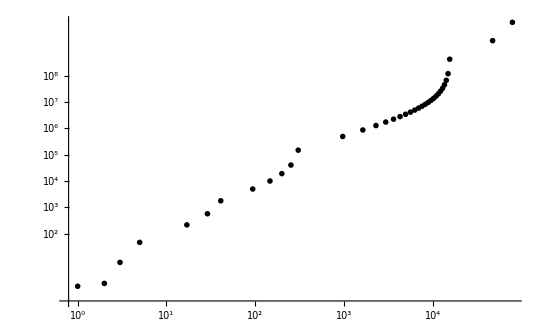

```mathematica
Show[resplotbw]
```

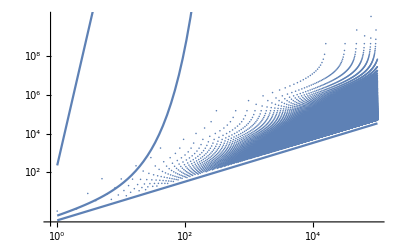

```mathematica
Show[resdotsplot,lowerboundplot,ellisonplot,rhinplot]
```

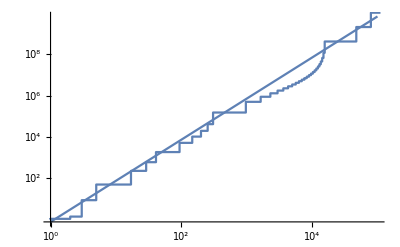

```mathematica
Show[diophantineplot,resplot]
```

Pushing it to x=11,000,000. (NB: This takes hours!)

```mathematica
(* maxb=11000000
```

As we increase x from 1 to 10,000,000, let’s record each loop that establishes a new “record” for altitude.

```mathematica
(* res11m=Nest[Updater,{1,3,1/2,Log[2,3],1,{{1,1}}},maxb-1][[6]]
```

```mathematica
(* resplot=ListPlot[res11m,ScalingFunctions->{"Log10","Log10"},PlotTheme->"GrayColor"];
```

```mathematica
(* diophantineplot=Plot[(x Log[2,3.])^2 /2.,{x,1,maxb},ScalingFunctions->{"Log10","Log10"},PlotTheme->"GrayColor"];
```

```mathematica
(* lowerboundplot=Plot[x/12.,{x,1,maxb},ScalingFunctions->{"Log10","Log10"},PlotTheme->"GrayColor"];
```

```mathematica
(* rhinplot=Plot[(x/2) x^13.3 / 0.00220823 ,{x,1,20},ScalingFunctions->{"Log10","Log10"},PlotTheme->"GrayColor"];
```

```mathematica
(* ellisonplot=Plot[(x/2) 1.17^x,{x,1,1000},ScalingFunctions->{"Log10","Log10"},PlotTheme->"GrayColor"];
```

x-axis:  number of up-moves x
y-axis:  altitude of highest/lowest loop with up-moves <= x

The solid jagged line shows the cumulative “record-holders” for loops with highest altitude.

```mathematica
(* Show[resplot,diophantineplot,lowerboundplot,rhinplot]
```

### Notes and References

```mathematica
12*20*20*18*20+9*20*18+ 13*20+1
```

1731501

```mathematica
13*20*20*18*20
```

1872000

```mathematica
13*20*20*18*20/365.366
```

5123.63

```mathematica
5125.6-(3113+(222/365))
```

2011.99

## Chapter 13. What can compute 3n+1?

### De Mol’s tag system

```mathematica
DeMol[pattern_]:=With[{a=Rest[Rest[pattern]],b=First[pattern]},Switch[b,0,Join[a,{1,2}],1,Join[a,{0}],2,Join[a,{0,0,0}]]]
```

```mathematica
DeMol[{0,0,0,0,0,0}]
```

{0,0,0,0,1,2}

```mathematica
ArrayPlot[NestList[DeMol,{0,0,0,0,0,0},10],ColorRules->{0->Black,1->Gray,2->LightGray}]
```

-Graphics-

### An amazing assault on the 3n+1 problem

```mathematica
f[n_]:=2n
```

```mathematica
t[n_]:=2n+1
```

```mathematica
o[n_]:=3n
```

```mathematica
i[n_]:= 3n+1
```

```mathematica
z[n_]:=3n+2
```

```mathematica
l[n_]:= 1
```

```mathematica
r[n_]:=n
```

```mathematica
fm[{x1_,x2_}]:={{1,1},{1,0}}.{x1,x2}
```

```mathematica
tm[{x1_,x2_}]:={{1,3},{3,4}}.{x1,x2}+{1,1}
```

```mathematica
om[{x1_,x2_}]:={{7,2},{2,5}}.{x1,x2}+{1,0}
```

```mathematica
im[{x1_,x2_}]:={{2,1},{1,1}}.{x1,x2}+{1,0}
```

```mathematica
zm[{x1_,x2_}]:={{2,2},{2,4}}.{x1,x2}+{0,2}
```

```mathematica
lm[{x1_,x2_}]:={{1,5},{0,0}}.{x1,x2}
```

```mathematica
rm[{x1_,x2_}]:={2,2}
```

```mathematica
lm[tm[rm[{0,0}]]]
```

{84,0}

```mathematica
{{"<t>", r[t[l[0]]], lm[tm[rm[{0,0}]]]},{"<2>",r[z[l[0]]],lm[zm[rm[{0,0}]]]},{"<ft>",r[t[f[l[0]]]],lm[fm[tm[rm[{0,0}]]]]},{"<f2>",r[z[f[l[0]]]],lm[fm[zm[rm[{0,0}]]]]},{"<1f>",r[f[i[l[0]]]],lm[im[fm[rm[{0,0}]]]]},{"<1>",r[i[l[0]]],lm[im[rm[{0,0}]]]},{"<ff>",r[f[f[l[0]]]],lm[fm[fm[rm[{0,0}]]]]},{"<f>",r[f[l[0]]],lm[fm[rm[{0,0}]]]},{"<>",r[l[0]],lm[rm[{0,0}]]}}
```

{{<t>,3,{84,0}},{<2>,5,{78,0}},{<ft>,5,{69,0}},{<f2>,8,{62,0}},{<1f>,8,{41,0}},{<1>,4,{27,0}},{<ff>,4,{26,0}},{<f>,2,{14,0}},{<>,1,{12,0}}}

### A cellular automaton

```mathematica
BaseForm[FromDigits["341",6],10]
```

133

```mathematica
KorecTable={{6,6,6,1,1,2,2},{6,0,0,1,1,2,2},{4,3,3,4,4,5,5},{6,0,0,1,1,2,2},{4,4,4,4,4,5,5},{6,0,0,1,1,2,2},{4,3,3,4,4,5,5}}
```

{{6,6,6,1,1,2,2},{6,0,0,1,1,2,2},{4,3,3,4,4,5,5},{6,0,0,1,1,2,2},{4,4,4,4,4,5,5},{6,0,0,1,1,2,2},{4,3,3,4,4,5,5}}

```mathematica
KorecNext[pair_]:=With[{a=pair[[1]],b=pair[[2]]},Part[Part[KorecTable,If[a==6,1,a+2]],If[b==6,1,b+2]]]
```

```mathematica
KorecInitial={6,6,6,6,6,1,1,6,6,6,6,6,6,6,6,6,6,6,6,6,6}
```

{6,6,6,6,6,1,1,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

```mathematica
listify[a_,b_]:={a,b}
```

```mathematica
KorecNextState[state_]:=With[{a=AppendTo[Rest[state],First[state]]},Drop[Insert[Map[KorecNext,MapThread[listify,{state,a}]],6,1],-1]]
```

```mathematica
NestList[KorecNextState,KorecInitial, 20]
```

Set::write: Tag Rest in Rest[{6,6,6,6,6,1,1,6,6,6,«11»}] is Protected.

Set::write: Tag Rest in Rest[{6,6,6,6,6,6,3,4,6,6,«11»}] is Protected.

Set::write: Tag Rest in Rest[{6,6,6,6,6,6,1,5,6,6,«11»}] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

{{6,6,6,6,6,1,1,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,3,4,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,1,5,6,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,5,4,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,2,5,6,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,1,2,4,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,4,2,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,2,1,6,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,1,0,4,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,3,2,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,1,4,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,5,6,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,2,4,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,1,2,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,2,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,1,6,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,2,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,1,6,6,6,6,6,6,6,6},{6,6,6,6,6,6,6,6,6,6,6,6,6,4,6,6,6,6,6,6,6}}

### The Farkas rule

```mathematica
T[n_]:=If[EvenQ[n],n/2,(3n+1)/2]
```

```mathematica
Farkas[n_]:=Switch[Mod[n,6],0,n/2,1,(n-1)/3,2,n/2,3,(3n+1)/2,4,(n-1)/3,5,(3n+1)/2]
```

```mathematica
NestWhileList[Farkas,3,#!=1&]
```

{3,5,8,4,1}

```mathematica
NestWhileList[T,3,#!=1&]
```

{3,5,8,4,2,1}

```mathematica
NestWhileList[Farkas,7,#!=1&]
```

{7,2,1}

```mathematica
NestWhileList[T,7,#!=1&]
```

{7,11,17,26,13,20,10,5,8,4,2,1}

### The original Collatz rule

```mathematica
UnsameQorCutoff[z__]:=And[UnsameQ[z],Length[List[z]]<400]
```

```mathematica
FindLoops[rule_]:=Table[With[{u=NestWhileList[rule,m,UnsameQorCutoff,All]},If[And[First[u]==Last[u],First[u]==First[MinimalBy[u,Abs]]],u,Nothing]],{m,1,200}]
```

```mathematica
Original[n_]:=Switch[Mod[n,3],0,2n/3,1,(4n-1)/3,2,(4n+1)/3]
```

```mathematica
OriginalInv[n_]:=Switch[Mod[n,4],0,3n/2,1,(3n+1)/4,2,3n/2,3,(3n-1)/4]
```

```mathematica
NestList[Original, 4,10]
```

{4,5,7,9,6,4,5,7,9,6,4}

```mathematica
FindLoops[Original]
```

{{1,1},{2,3,2},{4,5,7,9,6,4},{44,59,79,105,70,93,62,83,111,74,99,66,44}}

```mathematica
NestList[Original, 8,100]
```

{8,11,15,10,13,17,23,31,41,55,73,97,129,86,115,153,102,68,91,121,161,215,287,383,511,681,454,605,807,538,717,478,637,849,566,755,1007,1343,1791,1194,796,1061,1415,1887,1258,1677,1118,1491,994,1325,1767,1178,1571,2095,2793,1862,2483,3311,4415,5887,7849,10465,13953,9302,12403,16537,22049,29399,39199,52265,69687,46458,30972,20648,27531,18354,12236,16315,21753,14502,9668,12891,8594,11459,15279,10186,13581,9054,6036,4024,5365,7153,9537,6358,8477,11303,15071,20095,26793,17862,11908}

```mathematica
NestList[OriginalInv, 8,100]
```

{8,12,18,27,20,30,45,34,51,38,57,43,32,48,72,108,162,243,182,273,205,154,231,173,130,195,146,219,164,246,369,277,208,312,468,702,1053,790,1185,889,667,500,750,1125,844,1266,1899,1424,2136,3204,4806,7209,5407,4055,3041,2281,1711,1283,962,1443,1082,1623,1217,913,685,514,771,578,867,650,975,731,548,822,1233,925,694,1041,781,586,879,659,494,741,556,834,1251,938,1407,1055,791,593,445,334,501,376,564,846,1269,952,1428}

### A barely expanding system

```mathematica
NearFlatUniverse[n_]:=Switch[Mod[n,5],0,n/5,1,(2n+3)/5,2,(3n+4)/5,3,(521n+2)/5,4,(n+1)/5]
```

```mathematica
3126/3125.
```

1.00032

```mathematica
NestList[NearFlatUniverse, 3,70]
```

{3,313,32615,6523,679697,407819,81564,16313,1699815,339963,35424145,7084829,1416966,566787,340073,35435607,21261365,4252273,443086847,265852109,53170422,31902254,6380451,2552181,1020873,106374967,63824981,25529993,2660225271,1064090109,212818022,127690814,25538163,2661076585,532215317,319329191,127731677,76639007,45983405,9196681,3678673,383317727,229990637,137994383,14379014709,2875802942,1725481766,690192707,414115625,82823125,16564625,3312925,662585,132517,79511,31805,6361,2545,509,102,62,38,3960,792,476,191,77,47,29,6,3}

```mathematica
NestList[NearFlatUniverse, 4,20]
```

{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
NestList[NearFlatUniverse, 5,20]
```

{5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
NestList[NearFlatUniverse, 7,20]
```

{7,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
NestList[NearFlatUniverse, 8,20]
```

{8,834,167,101,41,17,11,5,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
NestList[NearFlatUniverse, 138324323434,100]
```

{138324323434,27664864687,16598918813,1729607340315,345921468063,36045016972165,7209003394433,751178153699919,150235630739984,30047126147997,18028275688799,3605655137760,721131027552,432678616532,259607169920,51921433984,10384286797,6230572079,1246114416,498445767,299067461,119626985,23925397,14355239,2871048,299163202,179497922,107698754,21539751,8615901,3446361,1378545,275709,55142,33086,13235,2647,1589,318,33136,13255,2651,1061,425,85,17,11,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
LoopsQ[n_,f_]:=Not[DuplicateFreeQ[NestList[f,n,1000]]]
```

```mathematica
NumbersThatReachALoop2[f_,upto_]:=Table[{n,LoopsQ[n,f]},{n,1,upto}]
```

```mathematica
TotalNumbersThatReachALoop2[f_,upto_]:=Length[Select[NumbersThatReachALoop2[f,upto],First[Rest[#]]==True&]]
```

```mathematica
T5[n_]:=If[EvenQ[n],n/2,(5n+1)/2]
```

```mathematica
Table[{i,TotalNumbersThatReachALoop2[NearFlatUniverse,i]/i*1.},{i,{100,1000}}]
```

{{100,0.91},{1000,0.858}}

```mathematica
Table[{i,TotalNumbersThatReachALoop2[T5,i]/i*1.},{i,{100,1000}}]
```

{{100,0.4},{1000,0.167}}

### 3n+1 without the +1

This is a hand-designed 30-way generalized 3n+1 rule that simulates 3n+1, but does it without any +1’s. All conditions replace n with a_i n.
  n = 375/2 n if n = {2, 8} mod 30
  n = 125/2 n if n = {0} mod 30
  n = 5/3 n if n = {3,9,15,21,27} mod 30
  n = 2/5 n if n = {5, 10, 20, 25} mod 30
  n = 3/4 n if n = {6,6,12,16,18,24} mod 30
The other 12 remainders are not used because they are never reached by any start number 2^n.

```mathematica
simulator30way[n_]:=With[{m=Mod[n,30]},If[MemberQ[{2,8},m],(375/2)n,If[MemberQ[{0},m],(125/2)n,If[MemberQ[{15,3,9,27,21},m],(5/3)n,If[MemberQ[{10,20,5,25},m],(2/5)n,If[MemberQ[{4,16,6,12,18,24},m],(3/4)n,0]]]]]]
```

```mathematica
NestList[simulator30way,2^3,96]
```

{8,1500,93750,5859375,9765625,3906250,1562500,625000,250000,100000,40000,16000,6400,2560,1024,768,576,432,324,243,405,675,1125,1875,3125,1250,500,200,80,32,6000,375000,23437500,1464843750,91552734375,152587890625,61035156250,24414062500,9765625000,3906250000,1562500000,625000000,250000000,100000000,40000000,16000000,6400000,2560000,1024000,409600,163840,65536,49152,36864,27648,20736,15552,11664,8748,6561,10935,18225,30375,50625,84375,140625,234375,390625,156250,62500,25000,10000,4000,1600,640,256,192,144,108,81,135,225,375,625,250,100,40,16,12,9,15,25,10,4,3,5,2}

```mathematica
Map[If[IntegerQ[Log[2,#]],Log[2,#],Nothing]&,NestList[simulator30way,2^3,96]]
```

{3,10,5,16,8,4,2,1}

```mathematica
Map[If[IntegerQ[Log[2,#]],Log[2,#],Nothing]&,NestList[simulator30way,2^31,202215]]
```

{31,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1}

### Properties of the 30-way rule

```mathematica
(375/2)^2 (125/2) (5/3)^5(2/5)^4(3/4)^6.
```

128746.

### Cycles revisited

```mathematica
OrderInvariantTuples[vals_,n_]:=With[{i={#2,#1,Length@vals}&@@@Partition[Prepend[Array[i,n],1],2,1]},Partition[vals[[Flatten[Table@@{i[[All,1]],Sequence@@i}]]],n]];
```

```mathematica
OrderInvariantTuples[{375/2,125/2,5/3,2/5,3/4},2]
```

Table::itraw: Raw object 4 cannot be used as an iterator.

Part::pkspec1: The expression Table[{4,7},{4,1,5},{7,4,5}] cannot be used as a part specification.

{375/2,125/2,5/3,2/5,3/4}⟦Table[{4,7},{4,1,5},{7,4,5}]⟧

```mathematica
Flatten[Table[Map[With[{m=Apply[Times,#]},If[m==1,{k,#},Nothing]]&,OrderInvariantTuples[{375/2,125/2,5/3,2/5,3/4},k]],{k,1,30}],1]
```

Table::itraw: Raw object 4 cannot be used as an iterator.

Part::pkspec1: The expression Table[{4},{4,1,5}] cannot be used as a part specification.

Thread::tdlen: Objects of unequal length in {4} {4,1,5} cannot be combined.

Part::pkspec1: The expression If[{4} {4,1,5}==1,{k,Table[{4},{4,1,5}]},Nothing] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Table::itraw: Raw object 4 cannot be used as an iterator.

Thread::tdlen: Objects of unequal length in {4,7} {4,1,5} {7,4,5} cannot be combined.

Table::itraw: Raw object 4 cannot be used as an iterator.

General::stop: Further output of Table::itraw will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

{Nothing⟦If[{4} {4,1,5}==1,{k,Table[{4},{4,1,5}]},Nothing]⟧,Nothing⟦If[{4,7} {4,1,5} {7,4,5}==1,{k,Table[{4,7},{4,1,5},{7,4,5}]},Nothing]⟧,Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[],Part[]}

### Monks’ simulator

```mathematica
monks={1/11,136/15,5/17,4/5,26/21,7/13,1/7,33/4,5/2,7/1}
```

{1/11,136/15,5/17,4/5,26/21,7/13,1/7,33/4,5/2,7}

```mathematica
generalAction[fractions_,n_]:=With[{f=SelectFirst[fractions,IntegerQ[#*n]&]},If[MissingQ[f],0,f*n]]
```

```mathematica
run[rule_,n_,iter_]:=Map[primeFactorForm,NestList[generalAction[rule,#]&,n,iter]]
```

```mathematica
monksAction[n_]:=generalAction[monks,n]
```

```mathematica
NestList[monksAction,2, 10]
```

{2,5,4,33,3,21,26,14,2,5,4}

```mathematica
NestList[monksAction,1021019, 10]
```

{1021019,7147133,1021019,7147133,1021019,7147133,1021019,7147133,1021019,7147133,1021019}

```mathematica
Map[If[IntegerQ[Log[2,#]],Log[2,#],Nothing]&,NestList[monksAction,2^7,500]]
```

{7,11,17,26,13,20,10,5,8,4,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2,1,2}

```mathematica
Length[NestWhileList[monksAction,2^7,#!=2^1&]]-1
```

258

```mathematica
Format[primeFactorForm[n_Integer]]:=CenterDot@@Superscript@@@FactorInteger[n]/. _[x_]:>x
```

```mathematica
Map[primeFactorForm,NestList[monksAction,2^7,100]]
```

{2^7,2^5·3^1·11^1,2^5·3^1,2^3·3^2·11^1,2^3·3^2,2^1·3^3·11^1,2^1·3^3,3^3·5^1,2^3·3^2·17^1,2^3·3^2·5^1,2^6·3^1·17^1,2^6·3^1·5^1,2^9·17^1,2^9·5^1,2^11,2^9·3^1·11^1,2^9·3^1,2^7·3^2·11^1,2^7·3^2,2^5·3^3·11^1,2^5·3^3,2^3·3^4·11^1,2^3·3^4,2^1·3^5·11^1,2^1·3^5,3^5·5^1,2^3·3^4·17^1,2^3·3^4·5^1,2^6·3^3·17^1,2^6·3^3·5^1,2^9·3^2·17^1,2^9·3^2·5^1,2^12·3^1·17^1,2^12·3^1·5^1,2^15·17^1,2^15·5^1,2^17,2^15·3^1·11^1,2^15·3^1,2^13·3^2·11^1,2^13·3^2,2^11·3^3·11^1,2^11·3^3,2^9·3^4·11^1,2^9·3^4,2^7·3^5·11^1,2^7·3^5,2^5·3^6·11^1,2^5·3^6,2^3·3^7·11^1,2^3·3^7,2^1·3^8·11^1,2^1·3^8,3^8·5^1,2^3·3^7·17^1,2^3·3^7·5^1,2^6·3^6·17^1,2^6·3^6·5^1,2^9·3^5·17^1,2^9·3^5·5^1,2^12·3^4·17^1,2^12·3^4·5^1,2^15·3^3·17^1,2^15·3^3·5^1,2^18·3^2·17^1,2^18·3^2·5^1,2^21·3^1·17^1,2^21·3^1·5^1,2^24·17^1,2^24·5^1,2^26,2^24·3^1·11^1,2^24·3^1,2^22·3^2·11^1,2^22·3^2,2^20·3^3·11^1,2^20·3^3,2^18·3^4·11^1,2^18·3^4,2^16·3^5·11^1,2^16·3^5,2^14·3^6·11^1,2^14·3^6,2^12·3^7·11^1,2^12·3^7,2^10·3^8·11^1,2^10·3^8,2^8·3^9·11^1,2^8·3^9,2^6·3^10·11^1,2^6·3^10,2^4·3^11·11^1,2^4·3^11,2^2·3^12·11^1,2^2·3^12,3^13·11^1,3^13,3^13·7^1,2^1·3^12·13^1,2^1·3^12·7^1,2^2·3^11·13^1}

### Fractran

```mathematica
universal= {583/559,629/551,437/527,82/517,615/329,371/129,1/115,53/86,43/53,23/47,341/46,41/43,47/41,29/37,37/31,299/29,47/23,161/15,527/19,159/7,1/17,1/13,1/3}
```

{583/559,629/551,437/527,82/517,615/329,371/129,1/115,53/86,43/53,23/47,341/46,41/43,47/41,29/37,37/31,299/29,47/23,161/15,527/19,159/7,1/17,1/13,1/3}

```mathematica
37485 * 2^(2^4)
```

2456616960

```mathematica
rununiversal[c_,n_,iter_]:=Map[primeFactorForm,NestList[generalAction[universal,#]&,c*2^(2^n),iter]]
```

```mathematica
rununiversal2[c_,n_,iter_]:=NestList[generalAction[universal,#]&,c*2^(2^n),iter]
```

```mathematica
rununiversal2[37485,3,187]
```

{9596160,102998784,763534464,633139584,4693491264,5601908928,4390685376,5012234304,3928507968,40504271808,300259927968,248982141408,1845715439568,2202950685936,1726637024112,1971061140048,1544885758416,15928304888496,118077216673416,97912227108696,725827596610116,866310357244332,679000009732044,775119793323876,607526324497092,6263805897401052,46433865456820842,38503983310494702,285431702366928117,340676547986333559,267016753827126303,304815858724614237,238909727108481429,2463241669152963699,5033580802182143211,798362912531790606,915196509487662402,145156893187598292,166399365361393164,26392162397745144,30254430065707848,4798574981408208,5500805466492336,872468178437856,1000146448453152,158630577897792,181844808809664,28841923254144,33062692510848,5243986046208,6011398638336,11237112956160,12881568510720,24079527763200,27603361094400,51598988064000,59150059488000,28945773792000,251702380800,2701605553920,23492222208,533609047296,432928094976,451515347712,366323772672,382051448064,309966269184,323274302208,262279150848,273539794176,221928512256,638259519744,517833195264,1489272212736,1208277455616,3474968496384,2819314063104,8108259824896,6578399480576,4054129912448,3289199740288,2027064956224,1644599870144,1013532478112,822299935072,506766239056,411149967536,253383119528,205574983768,126691559764,102787491884,63345779882,51393745942,31672889941,25696872971,24501669577,28087279759,4454849014,5106778138,809972548,928505116,147267736,168819112,26775952,30694384,57377040,65773680,122950800,140943600,263466000,302022000,564570000,647190000,316710000,2754000,29559600,257040,2758896,20451816,16959096,125718516,150051132,117607644,134256276,105227892,1084935852,8042676642,6669164502,49438806417,59007607659,46249206003,52796280537,41380868529,426651023799,871852092111,138282150006,158518562202,25142209092,28821556764,4571310744,5240283048,831147408,952778736,1781030160,2041668720,3816493200,4375004400,2140959600,18617040,199822896,1481295816,1228323096,9105612516,10867989132,8518153644,9723990276,7621505892,78580353852,582519579642,483038057502,3580782121917,4273836726159,3349763920503,3823959176037,2997157192029,30901724152299,63147001528611,10015578579006,11481273005202,1821014287092,2087504182764,331093506744,379546215048,60198819408,69008402736,128997470160,147875148720,72364434480,629255952,37015056,2847312,219024,16848,1296,432,144,48,16}

```mathematica
rununiversal[37485,3,3]
```

{2^8·3^2·5^1·7^2·17^1,2^8·3^1·7^3·17^1·23^1,2^7·3^1·7^3·11^1·17^1·31^1,2^7·3^1·7^3·11^1·19^1·23^1}

```mathematica
rununiversal2[2268945,1,400]
```

{9075780,97413372,722129562,861896574,675540558,6965056098,51632263683,61625605041,48301149897,498001511007,1017655261623,161407604358,185028229386,29346837156,33641496252,62886079620,72088920540,134755884900,154476258300,288762610500,331020553500,618777022500,709329757500,1325950762500,1519992337500,2841323062500,3257126437500,1593912937500,13860112500,148765207500,1293610500,13884752700,120736980,1295910252,9606639042,11465988534,8986855878,92657583018,686874691503,819818180181,642560195277,6625017185787,13538078597043,2147238771678,2461468835826,390407049396,447539788332,836586534420,959013832140,1792685430900,2055029640300,3841468780500,4403634943500,2154970291500,18738872100,201130560540,1748961396,39726408852,32230860012,33614653644,27272266164,28443168468,23076532908,24067296396,19526297076,20364635412,16522251372,47517482628,38551919868,110874126132,89954479692,258706294308,209893785948,603648020052,489752167212,1408512046788,1142755056828,3286528109172,2666428465932,7668565588068,6221666420508,17893319705492,14517221647852,8946659852746,7258610823926,4473329926373,3629305411963,3460500509081,3966915217727,629181910742,721257312314,114396711044,131137693148,20799402008,23843216936,3781709456,4335130352,8103663120,9289565040,17364992400,19906210800,37210698000,42656166000,79737210000,91406070000,170865450000,195870150000,366140250000,419721750000,784586250000,899403750000,1681256250000,1927293750000,943143750000,8201250000,88026750000,765450000,8215830000,71442000,766810800,6667920,71569008,530544168,633230136,496315512,5117184072,37933908012,45275954724,35486559108,365878661148,2712274422858,3237230762766,2537288976222,26160324272082,193927621234347,231461999537769,181416161799873,1870463185453863,3822250857231807,606237079870422,694954701314874,110224923612804,126355400239068,20040895202328,22973709134376,3643799127696,4177038024432,7808140987920,8950795766640,16731730688400,19180276642800,35853708618000,41100592806000,76829375610000,88072698870000,43099405830000,374777442000,4022611210800,34979227920,375443713008,2783180568168,3321860678136,2603620531512,26844225480072,198997410624012,237513038486724,186158868003108,1919362121825148,14228314859616858,16982182251800766,13310359062222222,137234391710498082,1017324512462605347,1214226031003754769,951690672948888873,9812259007300612863,20051137971440382807,3180257860073716422,3645661449352796874,578228701831584804,662847536245963068,105132491242106328,120517733862902376,19114998407655696,21912315247800432,40960710873547920,46954961245286640,87772951871888400,100617774097042800,49238485196425200,428160740838480,4595591951666352,34067322946048392,40660998354960984,31869431143077528,328584824544144168,2435813590642460028,2907261382379710356,2278664326730043252,23493814954906308012,174160671730935892002,207869188840149290454,162924499361198092518,1679807769275801022858,12452488028761916278143,14862647002070674267461,11649101704325663615037,120106255503219773134347,245434522115275188578883,38927719174956606312318,44624458566413670650706,7077767122719382965876,8113537921166121936492,1286866749585342357432,1475188712939294897544,233975772651880428624,268216129625326345008,501376655682600918480,574748849197127882160,281260075139020027440,2445739783817565456,188133829524428112,14471833040340624,1113217926180048,85632148167696,6587088320592,506699101584,38976853968,2998219536,230632272,17740944,1364688,104976,34992,11664,3888,1296,432,144,48,16,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Chapter 14. What can 3n+1 compute?

### Rule 110

```mathematica
update[state_]:=MovingMap[If[((Part[#,1]==0)&&(#[[2]]==0)&&(#[[3]]==0))||((#[[1]]==1)&&(#[[2]]==0)&&(#[[3]]==0))||((#[[1]]==1)&&(#[[2]]==1)&&(#[[3]]==1)),0,1]&,
state,{3,Center},0]
```

```mathematica
ArrayPlot[NestList[update,IntegerDigits[RandomInteger[2^1000],2,1000],500],ColorRules->{0->White,1->Black}, ColorFunction->"Rainbow"]
```

-Graphics-

### Engineering a 3n+1 behavior

```mathematica
T[n_,q_]:=If[EvenQ[n],n/2,(q*n+1)/2]
```

```mathematica
ArrayPlot[Map[IntegerDigits[#,2,50]&,NestList[T[#,3]&,398902141,100]],ColorRules->{0->White,1->Black},ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
ArrayPlot[Map[IntegerDigits[#,2,50]&,NestList[T[#,3]&,308728191,100]],ColorRules->{0->White,1->Black},ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
((128 *1)+1)/2187 * 128 - 1
```

4775/729

```mathematica
Reduce[2187c - 128d== 1,{c},Integers]
```

C[1]∈ℤ&&d==598+2187 C[1]&&c==35+128 C[1]

```mathematica
Table[{f, 35 + 128f,598+2187f},{f,0,5}]
```

{{0,35,598},{1,163,2785},{2,291,4972},{3,419,7159},{4,547,9346},{5,675,11533}}

```mathematica
163*2^7-1
```

20863

```mathematica
ArrayPlot[Map[IntegerDigits[#,2,50]&,NestList[T[#,3]&,20863,20]],ColorRules->{0->White,1->Black},ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
Reduce[5b-3c==1,PositiveIntegers]
```

False

```mathematica
Reduce[9b-6c==1,PositiveIntegers]
```

False

```mathematica
With[{x=2187,y=128},NestWhileList[If[#[[1]]>#[[2]],{Mod[#[[1]],#[[2]]],#[[2]]},{#[[1]],Mod[#[[2]],#[[1]]]}]&,{x,y},And[#[[1]]!=0,#[[2]]!=0,#[[1]]!=#[[2]]]&]]
```

{{2187,128},{11,128},{11,7},{4,7},{4,3},{1,3},{1,0}}

```mathematica
Reduce[11c-128d==1,PositiveIntegers]
```

C[1]∈ℤ&&C[1]≥0&&c==35+128 C[1]&&d==3+11 C[1]

```mathematica
Reduce[2187c-128d==1,PositiveIntegers]
```

C[1]∈ℤ&&C[1]≥0&&c==35+128 C[1]&&d==598+2187 C[1]

```mathematica
Reduce[7c-11d==1,PositiveIntegers]
```

C[1]∈ℤ&&C[1]≥0&&c==8+11 C[1]&&d==5+7 C[1]

```mathematica
Reduce[11c-7d==1,PositiveIntegers]
```

C[1]∈ℤ&&C[1]≥0&&c==2+7 C[1]&&d==3+11 C[1]

### Other behaviors

```mathematica
T[n_,q_]:=If[EvenQ[n],n/2,(3n+1)/2]
```

```mathematica
ArrayPlot[Map[IntegerDigits[#,2,600]&,NestList[T[#,3]&,2^328-1,328]],ColorRules->{0->White,1->Black},ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
ArrayPlot[Map[IntegerDigits[#,2,600]&,NestList[T[#,3]&,2^328-42,328]],ColorRules->{0->White,1->Black},ColorFunction->"Rainbow"]
```

-Graphics-

-Graphics-

```mathematica
ArrayPlot[Map[IntegerDigits[#,2,600]&,NestList[T[#,3]&,2^328-42,2000]],ColorRules->{0->White,1->Black},ColorFunction->"Rainbow"]
```

-Graphics-

### A universal computer can simulate itself

```mathematica
Log[10,2^(2^16.)]
```

19728.3017958347

```mathematica
Log[2,Log[2,2^(2^16)]]
```

16

### Practice gliders for 3n+1

```mathematica
T[n_]:=If[EvenQ[n],n/2,(3n+1)/2]
```

```mathematica
(* Flatten[Table[Table[With[{a=NestWhileList[T,n,(#!=1)&&(#!=m*n)&]},If[Last[a]==1,Nothing,{n,n*m,Length[a]-1,BaseForm[n,m],BaseForm[n*m,m]}]],{n,1,100000}],{m,3,13}],1]
```

```mathematica
(* Flatten[Table[Table[With[{a=NestWhileList[T,n,(#!=1)&&(#!=m*n)&]},If[Last[a]==1,Nothing,{n,n*m,Length[a]-1,BaseForm[n,m],BaseForm[n*m,m]}]],{n,1,100000}],{m,3,100}],1]
```

```mathematica
(* Flatten[Table[Table[With[{a=NestWhileList[T,n,(#!=1)&&(#!=m*n)&]},If[Last[a]==1,Nothing,{n,n*m,Length[a]-1,BaseForm[n,m],BaseForm[n*m,m]}]],{n,1,1000000}],{m,3,23}],1]
```

```mathematica
Map[BaseForm[#,10]&,NestList[T,671,32]]
```

{671,1007,1511,2267,3401,5102,2551,3827,5741,8612,4306,2153,3230,1615,2423,3635,5453,8180,4090,2045,3068,1534,767,1151,1727,2591,3887,5831,8747,13121,19682,9841,14762}

```mathematica
Map[BaseForm[#,22]&,NestList[T,671,32]]
```

{(18b)_22,(21h)_22,(32f)_22,(4f1)_22,(70d)_22,abk_22,(55l)_22,(7jl)_22,bil_22,hha_22,(8jg)_22,(49j)_22,(6ei)_22,379_22,503_22,(7b5)_22,b5j_22,gji_22,(89k)_22,(44l)_22,(67a)_22,(33g)_22,(1cj)_22,287_22,(3cb)_22,(57h)_22,(80f)_22,c11_22,i1d_22,1529_22,(1iee)_22,k77_22,(18b0)_22}

```mathematica
Map[BaseForm[#,10]&,NestList[T,1342,33]]
```

{1342,671,1007,1511,2267,3401,5102,2551,3827,5741,8612,4306,2153,3230,1615,2423,3635,5453,8180,4090,2045,3068,1534,767,1151,1727,2591,3887,5831,8747,13121,19682,9841,14762}

```mathematica
Map[BaseForm[#,11]&,NestList[T,1342,33]]
```

{1010_11,560_11,836_11,1154_11,1781_11,2612_11,3919_11,(1a0a)_11,(296a)_11,(434a)_11,(651a)_11,3265_11,1688_11,2477_11,1239_11,1903_11,2805_11,4108_11,6167_11,3089_11,(159a)_11,(233a)_11,1175_11,638_11,957_11,1330_11,(1a46)_11,(2a14)_11,4421_11,6632_11,9949_11,13873_11,7437_11,10100_11}

### Pay attention to nature

```mathematica
T[n_]:=If[EvenQ[n],n/2,(3n+1)/2]
```

```mathematica
ToBase10Big[x_]:=IntegerDigits[x,10,55]
```

```mathematica
myplot=Table[ArrayPlot[Map[ToBase10Big,b=NestWhileList[T,a=RandomInteger[10^50],#>1&]],ColorRules->{0->White},ColorFunction->"GrayLevel"],{x,1,20}];
```

ArrayPlot::cfun: Value of option ColorFunction -> GrayLevel is not a valid color function, or a gradient ColorData entity.

General::stop: Further output of ArrayPlot::cfun will be suppressed during this calculation.

```mathematica
ResourceFunction["PlotGrid"][{myplot}]
```

-Graphics-

### Notes and references

```mathematica
Solve[Mod[n,3]==2 && Mod[n,5]==3 && Mod[n,7]==2,{n},PositiveIntegers]
```

{{n→ConditionalExpression[23+105 C[1], C[1]∈ℤ&&C[1]≥0]}}

## Epilogue

```mathematica
Solve[18x-7y==35,{x,y},PositiveIntegers]
```

{{x→ConditionalExpression[7 C[1], C[1]∈ℤ&&C[1]≥1],y→ConditionalExpression[-5+18 C[1], C[1]∈ℤ&&C[1]≥1]}}

```mathematica
Table[{k, Floor[k / Log[2,3]],2^k-3^(Floor[k / Log[2,3]]),k^1.8},{k,2,20}]
```

{{2,1,1,3.4822},{3,1,5,7.22467},{4,2,7,12.1257},{5,3,5,18.1195},{6,3,37,25.1578},{7,4,47,33.2029},{8,5,13,42.2243},{9,5,269,52.1959},{10,6,295,63.0957},{11,6,1319,74.9043},{12,7,1909,87.6045},{13,8,1631,101.181},{14,8,9823,115.619},{15,9,13085,130.907},{16,10,6487,147.033},{17,10,72023,163.986},{18,11,84997,181.757},{19,11,347141,200.335},{20,12,517135,219.712}}

```mathematica
{Sum[2^i 3^(x-i-1),{i,0,x-1}],Sum[2^i 5^(x-i-1),{i,0,x-1}]}
```

{-2^x+3^x,1/3 (-2^x+5^x)}

```mathematica
{Gamma[4],Gamma[4.5],Gamma[5]}
```

{6,11.6317,24}

```mathematica
smoothed[x_]:=x+ 1/4-((2x+1)/4 )* Cos[Pi x]
```

```mathematica
{smoothed[7],smoothed[7.5],smoothed[8]}
```

{11,7.75,4}

```mathematica
NestList[smoothed,7,13]
```

{7,11,17,26,13,20,10,5,8,4,2,1,2,1}

```mathematica
NestList[smoothed,7.5,20]
```

{7.5,7.75,5.08318,8.02999,4.03392,2.02981,1.02045,2.02911,1.01984,2.02828,1.01913,2.02732,1.01831,2.02621,1.01739,2.02495,1.01635,2.02352,1.01521,2.02194,1.01397}

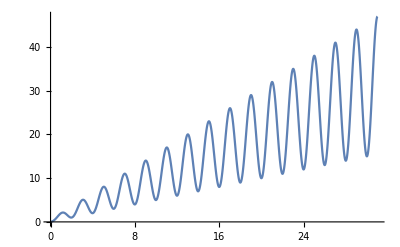

```mathematica
Plot[smoothed[x],{x,0,31}]
```